Construction and study of the ground state in the generalized Ising model

Grabovskiy Andrey

Espigule-Pons Bernat

Budker Institute and Novosibirsk State University

Most representative image

-Graphics-

Abstract

GOAL OF THE PROJECT: The goal of the project is to understand what kind of ground states are realized for a generalized Ising model with a given set of energy weights.

SUMMARY OF WORK: 1. Starting from random distributions states with local minimal energy were obtained via Monte Carlo and Cellular automaton techniques.  2. Exhaustive search for small field sizes was done.

RESULTS AND FUTURE  WORK: Fields with even number of states have regular symmetric ground states, fields with odd number of spins may have irregular ground states with high degeneracy.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

The 2 D Ising model is a system of interacting spins placed in the integer points of a rectangular grid. The energy of the system s is given by the list convolution of the weight pattern and the list of spin values s
e[s_, patternNum_] := Apply[Plus, s ListConvolve[pattern, s, 2], {0, 1}]
The weight pattern is defined as 1/2(w4 | w1 | w3
w2 | 0 | w2
w3 | w1 | w4) and the values for w’s ∈ {-2,-1,0,1,2}.
For the a 5x5 matrix s = d_ij for example this convolution reads
e =w1 (d_11 d_21+d_31 d_21+d_12 d_22+d_13 d_23+d_14 d_24+d_22 d_32+d_23 d_33+d_24 d_34+d_11 d_41+d_31 d_41+d_12 d_42+d_32 d_42+d_13 d_43+d_33 d_43+d_14 d_44+d_34 d_44)+w2 (d_11 d_12+d_13 d_12+d_11 d_14+d_13 d_14+d_21 d_22+d_22 d_23+d_21 d_24+d_23 d_24+d_31 d_32+d_32 d_33+d_31 d_34+d_33 d_34+d_41 d_42+d_42 d_43+d_41 d_44+d_43 d_44)+w3 (d_12 d_21+d_34 d_21+d_13 d_22+d_14 d_23+d_11 d_24+d_22 d_31+d_23 d_32+d_24 d_33+d_14 d_41+d_32 d_41+d_11 d_42+d_33 d_42+d_12 d_43+d_34 d_43+d_13 d_44+d_31 d_44)+w4 (d_14 d_21+d_32 d_21+d_11 d_22+d_12 d_23+d_13 d_24+d_24 d_31+d_22 d_33+d_23 d_34+d_12 d_41+d_34 d_41+d_13 d_42+d_31 d_42+d_14 d_43+d_32 d_43+d_11 d_44+d_33 d_44)

Exhaustive search for ground state on 3x3, 4x4. 5x5, 6x6 fields with periodic boundary conditions.

For example for interaction pattern (0 | 1 | 0
2 | 0 | 2
0 | 1 | 0)  up to rotations and black to white exchange there are 

3x3 	7 states with energy per spin = -2    

4x4      1 state  with energy per spin = -6      

5x5      51 states with energy per spin = -3.6 


	

6x6 	1 state with energy per spin = -6

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Detail

1. A manipulate demonstrating evolution of the system from a randomly generated state to a local minimum energy state via Monte Carlo (MC) algorithm is done for one of the weights.
2. Final states of such evolution were built for systems with all possible weights  w’s ∈ {-2,-1,0,1,2}.
3. 2 cellular automata (CA) which do not locally increase energy in evolution were constracted for systems with nearest neighbour (NN) interaction (w3=w4=0). Manipulates showing this evolution were built all such systems. One of them is shown to be globally energy reducing (nonincreasing). 
4-6. Exhaustive search of the ground state for 3x3 (NN), 4x4, and 5x5 (NN) was done.
7. For 6x6 field only few cases were investigated because of the large computation time. Their ground states read (0 | 1 | 0
2 | 0 | 2
0 | 1 | 0)-> ,(0 | 2 | 1
1 | 0 | 1
1 | 2 | 0)-> ,(0 | 1 | 0
2 | 0 | 2
0 | 1 | 0)-> . (to be checked)
8. A tooltip with the 4x4 ground state was built for the pictures of MC obtained local minima.

Code

## 1.Monte Carlo search for minimal energy configuration

```mathematica
ClearAll[n,field,m,w1,w2,w3,w4,Δe1,position,positions,op];

n=2^6;field=RandomInteger[1,{n,n}]/. 0->-1;w1=2;w2=2;w3=0;w4=0;

Δe1=
position↦((field⟦Mod[#1-1,n,1],Mod[#2+1,n,1]⟧+field⟦Mod[#1+1,n,1],Mod[#2-1,n,1]⟧)w4+(field⟦Mod[#1-1,n,1],Mod[#2-1,n,1]⟧+field⟦Mod[#1+1,n,1],Mod[#2+1,n,1]⟧)w3+(field⟦Mod[#1-1,n,1],#2⟧+field⟦Mod[#1+1,n,1],#2⟧)w1+w2 (field⟦#1,Mod[#2-1,n,1]⟧+field⟦#1,Mod[#2+1,n,1]⟧))field⟦#1,#2⟧&[Sequence@@position];
positions[m_]:=With[{position=RandomInteger[{1,n/m},2]},If[Or@@Flatten@Table[If[Δe1[{#1,#2}]>0,field⟦#1,#2⟧*=-1;True,False
]&[Mod[position⟦1⟧+n/m i,n,1],Mod[position⟦2⟧+n/m j,n,1]],{i,0,m-1},{j,0,m-1}],Sow[field]]]
```

```mathematica
ArrayPlot[field/.-1->0,PixelConstrained->2]
Monitor[op=Reap[Do[positions[16],{monitor,1,500}]]⟦2⟧;//AbsoluteTiming,monitor]
Tooltip[ArrayPlot[field/.-1->0,PixelConstrained->2],"{2,2,0,0}"]
Manipulate[ArrayPlot[op⟦1,l⟧/.-1->0,PixelConstrained->2],{l,1,Length[op⟦1⟧],1},SaveDefinitions->True]
```

-Graphics-

{3.19183,Null}

-Graphics-

```mathematica
Export["MC.gif",%36,"GIF"]
```

MC.gif

## 2. Monte Carlo evolution to for generalized Ising model with different weights

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\grabovsk\Google Drive\Works\Mathematica_Problems\Final_Project\Final-Project

```mathematica
ClearAll[m,w1,w2,w3,w4,Δe1,position,positions,Δe2,position,positions1];
field=RandomInteger[1,{n,n}]/. 0->-1;
Δe2[position_,w1_,w2_,w3_,w4_]:=((field⟦Mod[#1-1,n,1],Mod[#2+1,n,1]⟧+field⟦Mod[#1+1,n,1],Mod[#2-1,n,1]⟧)w3+(field⟦Mod[#1-1,n,1],Mod[#2-1,n,1]⟧+field⟦Mod[#1+1,n,1],Mod[#2+1,n,1]⟧)w4+(field⟦Mod[#1-1,n,1],#2⟧+field⟦Mod[#1+1,n,1],#2⟧)w1+w2 (field⟦#1,Mod[#2-1,n,1]⟧+field⟦#1,Mod[#2+1,n,1]⟧))field⟦#1,#2⟧&[Sequence@@position];
positions1[m_,w1_,w2_,w3_,w4_]:=With[{position=RandomInteger[{1,n/m},2]},Do[If[Δe2[{#1,#2},w1,w2,w3,w4]>0,field⟦#1,#2⟧*=-1;]&[Mod[position⟦1⟧+n/m i,n,1],Mod[position⟦2⟧+n/m j,n,1]],{i,0,m-1},{j,0,m-1}]]
```

```mathematica
result0=ParallelTable[(field=RandomInteger[1,{n,n}]/. 0->-1;Do[positions1[16,w1,w2,w3,w4],500];Print[i,w1,w2,w3,w4];ArrayPlot[field/.-1->0,PixelConstrained->2]->{w1,w2,w3,w4}),{w1,-2,2},{w2,-2,2},{w3,-2,2},{w4,-2,2},{i,1,5}];
```

12-2-2-2

11-2-2-2

1-2-2-2-2

10-2-2-2

22-2-2-2

21-2-2-2

20-2-2-2

2-2-2-2-2

32-2-2-2

31-2-2-2

3-2-2-2-2

30-2-2-2

41-2-2-2

42-2-2-2

4-2-2-2-2

40-2-2-2

51-2-2-2

52-2-2-2

5-2-2-2-2

50-2-2-2

12-2-2-1

11-2-2-1

1-2-2-2-1

10-2-2-1

22-2-2-1

21-2-2-1

2-2-2-2-1

20-2-2-1

31-2-2-1

32-2-2-1

3-2-2-2-1

30-2-2-1

42-2-2-1

41-2-2-1

4-2-2-2-1

40-2-2-1

52-2-2-1

51-2-2-1

5-2-2-2-1

50-2-2-1

12-2-20

11-2-20

1-2-2-20

10-2-20

22-2-20

21-2-20

2-2-2-20

20-2-20

32-2-20

31-2-20

3-2-2-20

30-2-20

41-2-20

42-2-20

4-2-2-20

40-2-20

51-2-20

52-2-20

5-2-2-20

50-2-20

11-2-21

12-2-21

1-2-2-21

10-2-21

21-2-21

22-2-21

2-2-2-21

20-2-21

31-2-21

32-2-21

3-2-2-21

30-2-21

41-2-21

42-2-21

4-2-2-21

40-2-21

51-2-21

52-2-21

5-2-2-21

50-2-21

11-2-22

12-2-22

1-2-2-22

10-2-22

21-2-22

22-2-22

2-2-2-22

20-2-22

31-2-22

32-2-22

3-2-2-22

41-2-22

30-2-22

42-2-22

4-2-2-22

52-2-22

40-2-22

51-2-22

5-2-2-22

12-2-1-2

50-2-22

11-2-1-2

22-2-1-2

1-2-2-1-2

21-2-1-2

10-2-1-2

32-2-1-2

2-2-2-1-2

31-2-1-2

20-2-1-2

42-2-1-2

41-2-1-2

3-2-2-1-2

30-2-1-2

52-2-1-2

51-2-1-2

40-2-1-2

4-2-2-1-2

12-2-1-1

11-2-1-1

50-2-1-2

5-2-2-1-2

22-2-1-1

21-2-1-1

10-2-1-1

1-2-2-1-1

32-2-1-1

31-2-1-1

20-2-1-1

2-2-2-1-1

42-2-1-1

41-2-1-1

3-2-2-1-1

30-2-1-1

52-2-1-1

51-2-1-1

4-2-2-1-1

40-2-1-1

12-2-10

11-2-10

5-2-2-1-1

50-2-1-1

22-2-10

21-2-10

1-2-2-10

10-2-10

32-2-10

31-2-10

2-2-2-10

20-2-10

42-2-10

41-2-10

3-2-2-10

30-2-10

52-2-10

51-2-10

4-2-2-10

12-2-11

40-2-10

11-2-11

22-2-11

5-2-2-10

50-2-10

21-2-11

32-2-11

1-2-2-11

10-2-11

31-2-11

42-2-11

2-2-2-11

41-2-11

20-2-11

52-2-11

3-2-2-11

51-2-11

30-2-11

12-2-12

4-2-2-11

11-2-12

40-2-11

22-2-12

21-2-12

5-2-2-11

50-2-11

32-2-12

31-2-12

1-2-2-12

10-2-12

42-2-12

41-2-12

2-2-2-12

20-2-12

52-2-12

51-2-12

3-2-2-12

30-2-12

12-20-2

11-20-2

4-2-2-12

40-2-12

22-20-2

21-20-2

5-2-2-12

50-2-12

32-20-2

31-20-2

1-2-20-2

10-20-2

42-20-2

41-20-2

2-2-20-2

20-20-2

52-20-2

51-20-2

30-20-2

3-2-20-2

12-20-1

11-20-1

40-20-2

4-2-20-2

22-20-1

21-20-1

50-20-2

5-2-20-2

32-20-1

31-20-1

10-20-1

1-2-20-1

42-20-1

41-20-1

20-20-1

2-2-20-1

52-20-1

51-20-1

30-20-1

3-2-20-1

12-200

11-200

4-2-20-1

40-20-1

22-200

21-200

32-200

5-2-20-1

50-20-1

31-200

42-200

1-2-200

10-200

41-200

52-200

2-2-200

20-200

51-200

12-201

3-2-200

11-201

30-200

22-201

21-201

4-2-200

40-200

32-201

31-201

5-2-200

50-200

42-201

41-201

1-2-201

10-201

52-201

51-201

2-2-201

20-201

12-202

11-202

3-2-201

30-201

22-202

21-202

4-2-201

32-202

40-201

31-202

5-2-201

42-202

50-201

41-202

1-2-202

52-202

10-202

51-202

2-2-202

12-21-2

20-202

11-21-2

22-21-2

3-2-202

30-202

21-21-2

32-21-2

4-2-202

31-21-2

40-202

42-21-2

5-2-202

41-21-2

50-202

52-21-2

1-2-21-2

51-21-2

10-21-2

12-21-1

2-2-21-2

11-21-1

20-21-2

22-21-1

3-2-21-2

21-21-1

30-21-2

32-21-1

4-2-21-2

31-21-1

40-21-2

42-21-1

5-2-21-2

41-21-1

50-21-2

52-21-1

1-2-21-1

51-21-1

10-21-1

12-210

2-2-21-1

11-210

20-21-1

22-210

3-2-21-1

21-210

30-21-1

32-210

4-2-21-1

31-210

40-21-1

42-210

5-2-21-1

41-210

50-21-1

52-210

1-2-210

51-210

12-211

10-210

11-211

2-2-210

22-211

20-210

21-211

3-2-210

32-211

30-210

31-211

4-2-210

42-211

40-210

41-211

5-2-210

52-211

50-210

51-211

1-2-211

12-212

10-211

11-212

22-212

2-2-211

20-211

32-212

21-212

3-2-211

30-211

42-212

31-212

4-2-211

40-211

52-212

41-212

5-2-211

50-211

12-22-2

51-212

1-2-212

10-212

22-22-2

11-22-2

2-2-212

20-212

32-22-2

21-22-2

3-2-212

30-212

42-22-2

31-22-2

4-2-212

40-212

52-22-2

41-22-2

5-2-212

50-212

12-22-1

51-22-2

1-2-22-2

10-22-2

22-22-1

11-22-1

2-2-22-2

20-22-2

32-22-1

21-22-1

3-2-22-2

30-22-2

42-22-1

31-22-1

4-2-22-2

40-22-2

52-22-1

41-22-1

5-2-22-2

50-22-2

12-220

51-22-1

1-2-22-1

10-22-1

22-220

11-220

2-2-22-1

20-22-1

32-220

21-220

3-2-22-1

30-22-1

42-220

31-220

4-2-22-1

52-220

40-22-1

41-220

5-2-22-1

12-221

50-22-1

51-220

1-2-220

22-221

10-220

11-221

2-2-220

32-221

20-220

21-221

3-2-220

42-221

30-220

31-221

4-2-220

52-221

40-220

41-221

12-222

5-2-220

50-220

51-221

22-222

1-2-221

10-221

11-222

32-222

2-2-221

20-221

21-222

42-222

3-2-221

30-221

31-222

52-222

4-2-221

40-221

41-222

12-1-2-2

5-2-221

50-221

51-222

22-1-2-2

1-2-222

10-222

11-1-2-2

32-1-2-2

2-2-222

20-222

21-1-2-2

42-1-2-2

3-2-222

30-222

31-1-2-2

52-1-2-2

4-2-222

40-222

41-1-2-2

12-1-2-1

5-2-222

51-1-2-2

50-222

22-1-2-1

1-2-1-2-2

11-1-2-1

10-1-2-2

32-1-2-1

2-2-1-2-2

21-1-2-1

20-1-2-2

42-1-2-1

3-2-1-2-2

31-1-2-1

30-1-2-2

52-1-2-1

4-2-1-2-2

41-1-2-1

40-1-2-2

12-1-20

5-2-1-2-2

51-1-2-1

50-1-2-2

22-1-20

1-2-1-2-1

11-1-20

10-1-2-1

32-1-20

2-2-1-2-1

21-1-20

20-1-2-1

42-1-20

3-2-1-2-1

31-1-20

30-1-2-1

52-1-20

41-1-20

4-2-1-2-1

40-1-2-1

12-1-21

51-1-20

5-2-1-2-1

50-1-2-1

22-1-21

11-1-21

1-2-1-20

10-1-20

32-1-21

21-1-21

2-2-1-20

20-1-20

42-1-21

31-1-21

3-2-1-20

52-1-21

30-1-20

41-1-21

4-2-1-20

12-1-22

40-1-20

51-1-21

5-2-1-20

22-1-22

50-1-20

11-1-22

1-2-1-21

32-1-22

10-1-21

21-1-22

2-2-1-21

42-1-22

20-1-21

31-1-22

3-2-1-21

52-1-22

30-1-21

41-1-22

4-2-1-21

12-1-1-2

40-1-21

51-1-22

22-1-1-2

5-2-1-21

50-1-21

11-1-1-2

32-1-1-2

1-2-1-22

10-1-22

21-1-1-2

42-1-1-2

2-2-1-22

20-1-22

31-1-1-2

52-1-1-2

3-2-1-22

30-1-22

41-1-1-2

12-1-1-1

4-2-1-22

40-1-22

51-1-1-2

22-1-1-1

5-2-1-22

50-1-22

11-1-1-1

32-1-1-1

1-2-1-1-2

10-1-1-2

21-1-1-1

42-1-1-1

20-1-1-2

2-2-1-1-2

31-1-1-1

52-1-1-1

30-1-1-2

3-2-1-1-2

41-1-1-1

12-1-10

40-1-1-2

4-2-1-1-2

51-1-1-1

22-1-10

50-1-1-2

5-2-1-1-2

11-1-10

32-1-10

1-2-1-1-1

10-1-1-1

21-1-10

42-1-10

2-2-1-1-1

20-1-1-1

31-1-10

52-1-10

30-1-1-1

3-2-1-1-1

41-1-10

12-1-11

40-1-1-1

4-2-1-1-1

51-1-10

22-1-11

50-1-1-1

5-2-1-1-1

32-1-11

11-1-11

10-1-10

1-2-1-10

42-1-11

21-1-11

20-1-10

2-2-1-10

52-1-11

31-1-11

30-1-10

3-2-1-10

12-1-12

41-1-11

40-1-10

4-2-1-10

22-1-12

51-1-11

50-1-10

11-1-12

5-2-1-10

32-1-12

21-1-12

42-1-12

10-1-11

1-2-1-11

31-1-12

52-1-12

20-1-11

2-2-1-11

12-10-2

41-1-12

30-1-11

3-2-1-11

22-10-2

51-1-12

40-1-11

4-2-1-11

32-10-2

11-10-2

5-2-1-11

50-1-11

42-10-2

21-10-2

1-2-1-12

10-1-12

52-10-2

31-10-2

2-2-1-12

20-1-12

12-10-1

41-10-2

3-2-1-12

30-1-12

22-10-1

51-10-2

4-2-1-12

40-1-12

32-10-1

11-10-1

5-2-1-12

50-1-12

42-10-1

21-10-1

1-2-10-2

10-10-2

52-10-1

31-10-1

2-2-10-2

20-10-2

12-100

41-10-1

30-10-2

3-2-10-2

22-100

51-10-1

40-10-2

4-2-10-2

32-100

11-100

50-10-2

5-2-10-2

42-100

21-100

10-10-1

1-2-10-1

52-100

31-100

20-10-1

2-2-10-1

12-101

41-100

30-10-1

3-2-10-1

22-101

51-100

40-10-1

4-2-10-1

32-101

11-101

50-10-1

5-2-10-1

42-101

21-101

10-100

1-2-100

52-101

31-101

12-102

20-100

2-2-100

41-101

22-102

30-100

3-2-100

51-101

32-102

40-100

4-2-100

11-102

42-102

50-100

5-2-100

21-102

52-102

10-101

1-2-101

31-102

12-11-2

20-101

2-2-101

41-102

22-11-2

30-101

3-2-101

51-102

32-11-2

40-101

4-2-101

11-11-2

42-11-2

50-101

5-2-101

21-11-2

52-11-2

1-2-102

10-102

31-11-2

12-11-1

2-2-102

20-102

41-11-2

22-11-1

3-2-102

30-102

51-11-2

32-11-1

40-102

4-2-102

11-11-1

42-11-1

50-102

5-2-102

21-11-1

52-11-1

10-11-2

1-2-11-2

31-11-1

12-110

2-2-11-2

41-11-1

20-11-2

22-110

3-2-11-2

51-11-1

30-11-2

32-110

11-110

40-11-2

4-2-11-2

42-110

21-110

5-2-11-2

50-11-2

52-110

31-110

10-11-1

1-2-11-1

12-111

41-110

20-11-1

2-2-11-1

22-111

51-110

30-11-1

3-2-11-1

32-111

11-111

40-11-1

4-2-11-1

42-111

21-111

52-111

50-11-1

5-2-11-1

31-111

12-112

1-2-110

10-110

41-111

22-112

20-110

2-2-110

51-111

32-112

30-110

3-2-110

11-112

42-112

40-110

4-2-110

21-112

52-112

50-110

5-2-110

31-112

12-12-2

10-111

1-2-111

41-112

22-12-2

20-111

2-2-111

32-12-2

51-112

3-2-111

30-111

42-12-2

11-12-2

4-2-111

40-111

52-12-2

21-12-2

50-111

5-2-111

12-12-1

31-12-2

10-112

1-2-112

22-12-1

41-12-2

2-2-112

20-112

32-12-1

51-12-2

30-112

3-2-112

42-12-1

11-12-1

4-2-112

40-112

52-12-1

21-12-1

5-2-112

50-112

12-120

31-12-1

1-2-12-2

10-12-2

22-120

41-12-1

2-2-12-2

32-120

20-12-2

51-12-1

3-2-12-2

42-120

30-12-2

11-120

4-2-12-2

52-120

40-12-2

21-120

12-121

5-2-12-2

31-120

50-12-2

22-121

1-2-12-1

10-12-1

41-120

32-121

2-2-12-1

51-120

20-12-1

42-121

3-2-12-1

11-121

30-12-1

52-121

4-2-12-1

21-121

40-12-1

12-122

31-121

5-2-12-1

50-12-1

22-122

41-121

1-2-120

10-120

32-122

51-121

2-2-120

20-120

42-122

11-122

3-2-120

30-120

52-122

21-122

4-2-120

40-120

120-2-2

31-122

5-2-120

50-120

220-2-2

41-122

1-2-121

10-121

320-2-2

51-122

2-2-121

20-121

420-2-2

110-2-2

3-2-121

30-121

520-2-2

210-2-2

4-2-121

40-121

120-2-1

310-2-2

5-2-121

50-121

220-2-1

410-2-2

1-2-122

10-122

320-2-1

510-2-2

20-122

2-2-122

420-2-1

110-2-1

3-2-122

30-122

520-2-1

210-2-1

4-2-122

120-20

40-122

310-2-1

5-2-122

220-20

50-122

410-2-1

320-20

1-20-2-2

100-2-2

510-2-1

420-20

2-20-2-2

200-2-2

110-20

520-20

3-20-2-2

300-2-2

210-20

120-21

4-20-2-2

400-2-2

310-20

220-21

5-20-2-2

500-2-2

410-20

320-21

100-2-1

1-20-2-1

510-20

420-21

200-2-1

2-20-2-1

110-21

520-21

300-2-1

3-20-2-1

210-21

120-22

400-2-1

310-21

4-20-2-1

220-22

500-2-1

410-21

5-20-2-1

320-22

510-21

100-20

1-20-20

420-22

110-22

2-20-20

200-20

520-22

210-22

3-20-20

300-20

120-1-2

310-22

4-20-20

400-20

220-1-2

410-22

5-20-20

500-20

320-1-2

510-22

1-20-21

420-1-2

100-21

110-1-2

520-1-2

2-20-21

200-21

210-1-2

120-1-1

3-20-21

300-21

310-1-2

220-1-1

4-20-21

400-21

410-1-2

320-1-1

5-20-21

500-21

510-1-2

420-1-1

1-20-22

100-22

110-1-1

520-1-1

2-20-22

200-22

210-1-1

120-10

3-20-22

300-22

310-1-1

220-10

4-20-22

400-22

410-1-1

320-10

5-20-22

500-22

510-1-1

420-10

1-20-1-2

100-1-2

110-10

520-10

2-20-1-2

210-10

200-1-2

120-11

3-20-1-2

310-10

300-1-2

220-11

4-20-1-2

410-10

320-11

400-1-2

5-20-1-2

510-10

420-11

500-1-2

1-20-1-1

520-11

110-11

100-1-1

2-20-1-1

120-12

210-11

200-1-1

3-20-1-1

220-12

310-11

300-1-1

4-20-1-1

320-12

410-11

400-1-1

5-20-1-1

420-12

510-11

500-1-1

1-20-10

520-12

110-12

100-10

1200-2

2-20-10

210-12

200-10

2200-2

3-20-10

310-12

300-10

3200-2

4-20-10

410-12

400-10

4200-2

5-20-10

510-12

500-10

5200-2

1-20-11

1100-2

100-11

2-20-11

1200-1

2100-2

200-11

2200-1

3-20-11

3100-2

300-11

3200-1

4-20-11

4100-2

400-11

4200-1

5-20-11

5100-2

500-11

5200-1

1-20-12

1100-1

100-12

12000

2-20-12

2100-1

200-12

22000

3-20-12

3100-1

300-12

32000

4-20-12

4100-1

400-12

42000

5-20-12

5100-1

500-12

52000

11000

1-200-2

1000-2

12001

21000

2-200-2

2000-2

22001

31000

3-200-2

32001

3000-2

41000

4-200-2

42001

4000-2

51000

5-200-2

52001

5000-2

11001

1-200-1

12002

1000-1

21001

2-200-1

22002

2000-1

31001

3-200-1

32002

3000-1

41001

4-200-1

42002

4000-1

51001

5-200-1

52002

5000-1

11002

1201-2

1-2000

10000

21002

2201-2

2-2000

31002

20000

3201-2

3-2000

41002

30000

4201-2

4-2000

51002

40000

5201-2

5-2000

1101-2

50000

1201-1

1-2001

2101-2

10001

2201-1

2-2001

3101-2

20001

3201-1

3-2001

4101-2

30001

4201-1

4-2001

5101-2

5201-1

40001

5-2001

1101-1

12010

50001

1-2002

2101-1

22010

10002

2-2002

3101-1

32010

20002

4101-1

3-2002

42010

30002

5101-1

4-2002

52010

40002

11010

12011

5-2002

50002

21010

22011

1-201-2

1001-2

31010

32011

2-201-2

2001-2

41010

42011

3-201-2

3001-2

51010

52011

4-201-2

4001-2

11011

12012

5-201-2

5001-2

21011

22012

1-201-1

1001-1

31011

32012

2-201-1

2001-1

41011

42012

3-201-1

51011

3001-1

52012

4-201-1

11012

4001-1

1202-2

5-201-1

21012

5001-1

2202-2

1-2010

31012

3202-2

10010

2-2010

41012

4202-2

20010

3-2010

51012

5202-2

30010

4-2010

1102-2

1202-1

40010

5-2010

2102-2

2202-1

50010

1-2011

3102-2

3202-1

10011

2-2011

4102-2

4202-1

20011

3-2011

5102-2

5202-1

30011

4-2011

1102-1

12020

40011

2102-1

5-2011

22020

50011

3102-1

1-2012

32020

10012

4102-1

2-2012

42020

20012

5102-1

3-2012

52020

30012

11020

12021

4-2012

40012

21020

22021

5-2012

50012

31020

32021

1-202-2

1002-2

41020

42021

2-202-2

2002-2

51020

52021

3-202-2

3002-2

11021

12022

4-202-2

4002-2

21021

22022

5-202-2

5002-2

31021

32022

1-202-1

1002-1

41021

42022

2-202-1

2002-1

51021

52022

3-202-1

3002-1

11022

121-2-2

4-202-1

4002-1

21022

221-2-2

5-202-1

31022

5002-1

321-2-2

1-2020

41022

10020

421-2-2

2-2020

51022

20020

521-2-2

3-2020

111-2-2

30020

121-2-1

4-2020

211-2-2

40020

221-2-1

5-2020

311-2-2

50020

321-2-1

1-2021

411-2-2

421-2-1

10021

2-2021

511-2-2

521-2-1

20021

3-2021

111-2-1

121-20

30021

4-2021

211-2-1

221-20

40021

5-2021

311-2-1

321-20

50021

1-2022

411-2-1

421-20

10022

2-2022

511-2-1

521-20

20022

3-2022

111-20

121-21

30022

4-2022

211-20

221-21

40022

5-2022

311-20

321-21

50022

1-21-2-2

411-20

421-21

101-2-2

511-20

2-21-2-2

521-21

201-2-2

111-21

3-21-2-2

121-22

301-2-2

211-21

4-21-2-2

221-22

401-2-2

311-21

5-21-2-2

321-22

501-2-2

411-21

1-21-2-1

421-22

101-2-1

511-21

2-21-2-1

521-22

201-2-1

111-22

3-21-2-1

121-1-2

301-2-1

211-22

4-21-2-1

221-1-2

401-2-1

311-22

5-21-2-1

321-1-2

411-22

501-2-1

1-21-20

421-1-2

511-22

101-20

521-1-2

2-21-20

111-1-2

201-20

3-21-20

121-1-1

211-1-2

301-20

221-1-1

4-21-20

311-1-2

401-20

321-1-1

5-21-20

411-1-2

501-20

421-1-1

1-21-21

511-1-2

521-1-1

101-21

2-21-21

111-1-1

121-10

201-21

3-21-21

211-1-1

221-10

301-21

4-21-21

311-1-1

321-10

401-21

5-21-21

411-1-1

421-10

501-21

1-21-22

511-1-1

521-10

2-21-22

101-22

111-10

121-11

3-21-22

201-22

211-10

221-11

4-21-22

301-22

311-10

321-11

5-21-22

401-22

411-10

421-11

1-21-1-2

501-22

511-10

521-11

2-21-1-2

101-1-2

121-12

111-11

3-21-1-2

201-1-2

221-12

211-11

4-21-1-2

321-12

301-1-2

311-11

5-21-1-2

421-12

401-1-2

411-11

1-21-1-1

521-12

511-11

501-1-2

2-21-1-1

1210-2

101-1-1

111-12

3-21-1-1

2210-2

211-12

201-1-1

4-21-1-1

3210-2

311-12

301-1-1

5-21-1-1

4210-2

411-12

401-1-1

5210-2

1-21-10

511-12

501-1-1

2-21-10

1210-1

1110-2

101-10

3-21-10

2210-1

2110-2

201-10

4-21-10

3210-1

3110-2

301-10

4210-1

5-21-10

4110-2

401-10

5210-1

1-21-11

5110-2

501-10

12100

1110-1

2-21-11

101-11

22100

2110-1

3-21-11

201-11

32100

3110-1

4-21-11

301-11

42100

4110-1

5-21-11

401-11

52100

5110-1

1-21-12

501-11

12101

11100

2-21-12

22101

101-12

21100

3-21-12

32101

201-12

31100

4-21-12

42101

301-12

41100

5-21-12

52101

401-12

51100

1-210-2

12102

501-12

11101

2-210-2

22102

1010-2

21101

3-210-2

32102

2010-2

31101

42102

4-210-2

3010-2

41101

52102

5-210-2

4010-2

51101

1211-2

1-210-1

11102

5010-2

2211-2

2-210-1

21102

1010-1

3211-2

3-210-1

31102

2010-1

4211-2

4-210-1

41102

3010-1

5211-2

5-210-1

51102

1211-1

4010-1

1-2100

1111-2

2211-1

5010-1

2-2100

2111-2

3211-1

10100

3-2100

3111-2

4211-1

20100

4-2100

4111-2

5211-1

30100

5-2100

5111-2

12110

40100

1-2101

1111-1

22110

50100

2-2101

2111-1

32110

10101

3111-1

3-2101

42110

20101

4111-1

4-2101

52110

30101

5111-1

5-2101

12111

40101

1-2102

11110

22111

50101

2-2102

21110

32111

10102

3-2102

31110

42111

20102

41110

52111

4-2102

30102

51110

12112

5-2102

40102

11111

22112

1-211-2

50102

32112

21111

2-211-2

42112

1011-2

31111

3-211-2

52112

41111

2011-2

4-211-2

1212-2

51111

3011-2

5-211-2

2212-2

11112

4011-2

1-211-1

3212-2

21112

5011-2

2-211-1

4212-2

31112

1011-1

3-211-1

5212-2

41112

2011-1

4-211-1

1212-1

51112

3011-1

5-211-1

2212-1

1112-2

4011-1

1-2110

3212-1

2112-2

4212-1

2-2110

5011-1

3112-2

5212-1

4112-2

3-2110

10110

12120

5112-2

4-2110

20110

22120

1112-1

5-2110

30110

2112-1

32120

1-2111

40110

3112-1

42120

2-2111

50110

4112-1

52120

3-2111

10111

5112-1

12121

4-2111

20111

11120

22121

5-2111

30111

21120

32121

1-2112

40111

31120

42121

2-2112

50111

52121

41120

3-2112

10112

12122

51120

4-2112

20112

22122

11121

5-2112

30112

32122

21121

1-212-2

42122

40112

31121

2-212-2

52122

50112

41121

3-212-2

122-2-2

1012-2

51121

4-212-2

222-2-2

2012-2

11122

5-212-2

322-2-2

3012-2

21122

1-212-1

422-2-2

4012-2

31122

522-2-2

2-212-1

5012-2

41122

122-2-1

3-212-1

1012-1

51122

222-2-1

4-212-1

2012-1

112-2-2

322-2-1

5-212-1

3012-1

212-2-2

422-2-1

1-2120

4012-1

312-2-2

522-2-1

2-2120

5012-1

412-2-2

122-20

3-2120

512-2-2

10120

222-20

4-2120

112-2-1

20120

322-20

5-2120

212-2-1

30120

422-20

1-2121

312-2-1

40120

522-20

2-2121

412-2-1

50120

122-21

3-2121

512-2-1

222-21

10121

4-2121

112-20

322-21

20121

5-2121

212-20

422-21

30121

1-2122

312-20

522-21

40121

2-2122

412-20

122-22

50121

3-2122

512-20

222-22

10122

4-2122

112-21

322-22

20122

5-2122

212-21

422-22

30122

312-21

1-22-2-2

522-22

40122

412-21

2-22-2-2

122-1-2

50122

512-21

3-22-2-2

222-1-2

102-2-2

112-22

4-22-2-2

322-1-2

202-2-2

212-22

422-1-2

5-22-2-2

302-2-2

312-22

522-1-2

1-22-2-1

402-2-2

412-22

122-1-1

2-22-2-1

502-2-2

512-22

222-1-1

3-22-2-1

102-2-1

112-1-2

322-1-1

4-22-2-1

202-2-1

212-1-2

422-1-1

5-22-2-1

302-2-1

312-1-2

522-1-1

1-22-20

402-2-1

412-1-2

122-10

2-22-20

502-2-1

512-1-2

222-10

3-22-20

112-1-1

102-20

322-10

4-22-20

212-1-1

202-20

422-10

5-22-20

312-1-1

302-20

522-10

1-22-21

412-1-1

402-20

122-11

2-22-21

512-1-1

222-11

502-20

3-22-21

112-10

322-11

102-21

4-22-21

212-10

422-11

202-21

5-22-21

312-10

522-11

302-21

1-22-22

122-12

412-10

402-21

2-22-22

512-10

222-12

502-21

3-22-22

112-11

322-12

102-22

4-22-22

422-12

212-11

202-22

5-22-22

522-12

312-11

302-22

1-22-1-2

1220-2

412-11

402-22

2-22-1-2

2220-2

502-22

512-11

3-22-1-2

3220-2

102-1-2

112-12

4-22-1-2

4220-2

202-1-2

212-12

5-22-1-2

5220-2

302-1-2

312-12

1-22-1-1

1220-1

402-1-2

412-12

2-22-1-1

2220-1

502-1-2

512-12

3-22-1-1

3220-1

102-1-1

1120-2

4-22-1-1

4220-1

202-1-1

2120-2

5-22-1-1

5220-1

302-1-1

3120-2

1-22-10

12200

402-1-1

4120-2

2-22-10

22200

502-1-1

5120-2

3-22-10

32200

1120-1

102-10

4-22-10

42200

2120-1

202-10

5-22-10

52200

302-10

3120-1

1-22-11

12201

402-10

4120-1

2-22-11

22201

502-10

5120-1

3-22-11

32201

102-11

11200

4-22-11

42201

202-11

5-22-11

21200

52201

302-11

1-22-12

31200

12202

402-11

2-22-12

41200

22202

502-11

3-22-12

51200

32202

102-12

4-22-12

11201

42202

202-12

5-22-12

21201

52202

302-12

1-220-2

31201

1221-2

402-12

2-220-2

41201

2221-2

502-12

3-220-2

51201

3221-2

1020-2

4-220-2

11202

4221-2

2020-2

5-220-2

21202

5221-2

3020-2

1-220-1

1221-1

31202

4020-2

2-220-1

2221-1

41202

3-220-1

5020-2

3221-1

51202

4-220-1

1020-1

4221-1

1121-2

5-220-1

2020-1

5221-1

2121-2

1-2200

3020-1

12210

3121-2

2-2200

4020-1

22210

4121-2

3-2200

5020-1

32210

5121-2

4-2200

10200

42210

1121-1

5-2200

20200

52210

1-2201

30200

2121-1

12211

40200

2-2201

3121-1

22211

50200

3-2201

4121-1

32211

10201

4-2201

5121-1

42211

20201

5-2201

11210

52211

30201

1-2202

21210

12212

2-2202

40201

31210

22212

50201

3-2202

41210

32212

4-2202

10202

51210

42212

5-2202

20202

11211

52212

1-221-2

30202

21211

1222-2

2-221-2

40202

31211

2222-2

3-221-2

50202

41211

3222-2

4-221-2

1021-2

51211

4222-2

5-221-2

2021-2

11212

5222-2

1-221-1

3021-2

21212

1222-1

2-221-1

4021-2

31212

2222-1

3-221-1

5021-2

41212

3222-1

4-221-1

1021-1

51212

4222-1

5-221-1

2021-1

1122-2

5222-1

1-2210

3021-1

2122-2

12220

2-2210

4021-1

3122-2

22220

3-2210

5021-1

4122-2

32220

4-2210

10210

5122-2

42220

5-2210

20210

1122-1

52220

1-2211

30210

2122-1

2-2211

12221

40210

3122-1

3-2211

22221

50210

4-2211

4122-1

32221

10211

5-2211

5122-1

42221

20211

1-2212

11220

52221

30211

2-2212

21220

40211

12222

3-2212

31220

50211

22222

4-2212

41220

32222

5-2212

10212

51220

42222

20212

1-222-2

30212

11221

52222

2-222-2

40212

21221

3-222-2

31221

50212

4-222-2

41221

1022-2

5-222-2

51221

2022-2

1-222-1

11222

3022-2

2-222-1

21222

4022-2

3-222-1

5022-2

31222

4-222-1

1022-1

41222

5-222-1

2022-1

51222

1-2220

3022-1

2-2220

4022-1

3-2220

5022-1

4-2220

10220

5-2220

20220

1-2221

30220

2-2221

40220

3-2221

50220

4-2221

10221

5-2221

20221

1-2222

30221

2-2222

40221

3-2222

50221

4-2222

10222

5-2222

20222

1-1-2-2-2

30222

2-1-2-2-2

40222

3-1-2-2-2

50222

4-1-2-2-2

5-1-2-2-2

1-1-2-2-1

2-1-2-2-1

3-1-2-2-1

4-1-2-2-1

5-1-2-2-1

1-1-2-20

2-1-2-20

3-1-2-20

4-1-2-20

5-1-2-20

1-1-2-21

2-1-2-21

3-1-2-21

4-1-2-21

5-1-2-21

1-1-2-22

2-1-2-22

3-1-2-22

4-1-2-22

5-1-2-22

1-1-2-1-2

2-1-2-1-2

3-1-2-1-2

4-1-2-1-2

5-1-2-1-2

1-1-2-1-1

2-1-2-1-1

3-1-2-1-1

4-1-2-1-1

5-1-2-1-1

1-1-2-10

2-1-2-10

3-1-2-10

4-1-2-10

5-1-2-10

1-1-2-11

2-1-2-11

3-1-2-11

4-1-2-11

5-1-2-11

1-1-2-12

2-1-2-12

3-1-2-12

4-1-2-12

5-1-2-12

1-1-20-2

2-1-20-2

3-1-20-2

4-1-20-2

5-1-20-2

1-1-20-1

2-1-20-1

3-1-20-1

4-1-20-1

5-1-20-1

1-1-200

2-1-200

3-1-200

4-1-200

5-1-200

1-1-201

2-1-201

3-1-201

4-1-201

5-1-201

1-1-202

2-1-202

3-1-202

4-1-202

5-1-202

1-1-21-2

2-1-21-2

3-1-21-2

4-1-21-2

5-1-21-2

1-1-21-1

2-1-21-1

3-1-21-1

4-1-21-1

5-1-21-1

1-1-210

2-1-210

3-1-210

4-1-210

5-1-210

1-1-211

2-1-211

3-1-211

4-1-211

5-1-211

1-1-212

2-1-212

3-1-212

4-1-212

5-1-212

1-1-22-2

2-1-22-2

3-1-22-2

4-1-22-2

5-1-22-2

1-1-22-1

2-1-22-1

3-1-22-1

4-1-22-1

5-1-22-1

1-1-220

2-1-220

3-1-220

4-1-220

5-1-220

1-1-221

2-1-221

3-1-221

4-1-221

5-1-221

1-1-222

2-1-222

3-1-222

4-1-222

5-1-222

1-1-1-2-2

2-1-1-2-2

3-1-1-2-2

4-1-1-2-2

5-1-1-2-2

1-1-1-2-1

2-1-1-2-1

3-1-1-2-1

4-1-1-2-1

5-1-1-2-1

1-1-1-20

2-1-1-20

3-1-1-20

4-1-1-20

5-1-1-20

1-1-1-21

2-1-1-21

3-1-1-21

4-1-1-21

5-1-1-21

1-1-1-22

2-1-1-22

3-1-1-22

4-1-1-22

5-1-1-22

1-1-1-1-2

2-1-1-1-2

3-1-1-1-2

4-1-1-1-2

5-1-1-1-2

1-1-1-1-1

2-1-1-1-1

3-1-1-1-1

4-1-1-1-1

5-1-1-1-1

1-1-1-10

2-1-1-10

3-1-1-10

4-1-1-10

5-1-1-10

1-1-1-11

2-1-1-11

3-1-1-11

4-1-1-11

5-1-1-11

1-1-1-12

2-1-1-12

3-1-1-12

4-1-1-12

5-1-1-12

1-1-10-2

2-1-10-2

3-1-10-2

4-1-10-2

5-1-10-2

1-1-10-1

2-1-10-1

3-1-10-1

4-1-10-1

5-1-10-1

1-1-100

2-1-100

3-1-100

4-1-100

5-1-100

1-1-101

2-1-101

3-1-101

4-1-101

5-1-101

1-1-102

2-1-102

3-1-102

4-1-102

5-1-102

1-1-11-2

2-1-11-2

3-1-11-2

4-1-11-2

5-1-11-2

1-1-11-1

2-1-11-1

3-1-11-1

4-1-11-1

5-1-11-1

1-1-110

2-1-110

3-1-110

4-1-110

5-1-110

1-1-111

2-1-111

3-1-111

4-1-111

5-1-111

1-1-112

2-1-112

3-1-112

4-1-112

5-1-112

1-1-12-2

2-1-12-2

3-1-12-2

4-1-12-2

5-1-12-2

1-1-12-1

2-1-12-1

3-1-12-1

4-1-12-1

5-1-12-1

1-1-120

2-1-120

3-1-120

4-1-120

5-1-120

1-1-121

2-1-121

3-1-121

4-1-121

5-1-121

1-1-122

2-1-122

3-1-122

4-1-122

5-1-122

1-10-2-2

2-10-2-2

3-10-2-2

4-10-2-2

5-10-2-2

1-10-2-1

2-10-2-1

3-10-2-1

4-10-2-1

5-10-2-1

1-10-20

2-10-20

3-10-20

4-10-20

5-10-20

1-10-21

2-10-21

3-10-21

4-10-21

5-10-21

1-10-22

2-10-22

3-10-22

4-10-22

5-10-22

1-10-1-2

2-10-1-2

3-10-1-2

4-10-1-2

5-10-1-2

1-10-1-1

2-10-1-1

3-10-1-1

4-10-1-1

5-10-1-1

1-10-10

2-10-10

3-10-10

4-10-10

5-10-10

1-10-11

2-10-11

3-10-11

4-10-11

5-10-11

1-10-12

2-10-12

3-10-12

4-10-12

5-10-12

1-100-2

2-100-2

3-100-2

4-100-2

5-100-2

1-100-1

2-100-1

3-100-1

4-100-1

5-100-1

1-1000

2-1000

3-1000

4-1000

5-1000

1-1001

2-1001

3-1001

4-1001

5-1001

1-1002

2-1002

3-1002

4-1002

5-1002

1-101-2

2-101-2

3-101-2

4-101-2

5-101-2

1-101-1

2-101-1

3-101-1

4-101-1

5-101-1

1-1010

2-1010

3-1010

4-1010

5-1010

1-1011

2-1011

3-1011

4-1011

5-1011

1-1012

2-1012

3-1012

4-1012

5-1012

1-102-2

2-102-2

3-102-2

4-102-2

5-102-2

1-102-1

2-102-1

3-102-1

4-102-1

5-102-1

1-1020

2-1020

3-1020

4-1020

5-1020

1-1021

2-1021

3-1021

4-1021

5-1021

1-1022

2-1022

3-1022

4-1022

5-1022

1-11-2-2

2-11-2-2

3-11-2-2

4-11-2-2

5-11-2-2

1-11-2-1

2-11-2-1

3-11-2-1

4-11-2-1

5-11-2-1

1-11-20

2-11-20

3-11-20

4-11-20

5-11-20

1-11-21

2-11-21

3-11-21

4-11-21

5-11-21

1-11-22

2-11-22

3-11-22

4-11-22

5-11-22

1-11-1-2

2-11-1-2

3-11-1-2

4-11-1-2

5-11-1-2

1-11-1-1

2-11-1-1

3-11-1-1

4-11-1-1

5-11-1-1

1-11-10

2-11-10

3-11-10

4-11-10

5-11-10

1-11-11

2-11-11

3-11-11

4-11-11

5-11-11

1-11-12

2-11-12

3-11-12

4-11-12

5-11-12

1-110-2

2-110-2

3-110-2

4-110-2

5-110-2

1-110-1

2-110-1

3-110-1

4-110-1

5-110-1

1-1100

2-1100

3-1100

4-1100

5-1100

1-1101

2-1101

3-1101

4-1101

5-1101

1-1102

2-1102

3-1102

4-1102

5-1102

1-111-2

2-111-2

3-111-2

4-111-2

5-111-2

1-111-1

2-111-1

3-111-1

4-111-1

5-111-1

1-1110

2-1110

3-1110

4-1110

5-1110

1-1111

2-1111

3-1111

4-1111

5-1111

1-1112

2-1112

3-1112

4-1112

5-1112

1-112-2

2-112-2

3-112-2

4-112-2

5-112-2

1-112-1

2-112-1

3-112-1

4-112-1

5-112-1

1-1120

2-1120

3-1120

4-1120

5-1120

1-1121

2-1121

3-1121

4-1121

5-1121

1-1122

2-1122

3-1122

4-1122

5-1122

1-12-2-2

2-12-2-2

3-12-2-2

4-12-2-2

5-12-2-2

1-12-2-1

2-12-2-1

3-12-2-1

4-12-2-1

5-12-2-1

1-12-20

2-12-20

3-12-20

4-12-20

5-12-20

1-12-21

2-12-21

3-12-21

4-12-21

5-12-21

1-12-22

2-12-22

3-12-22

4-12-22

5-12-22

1-12-1-2

2-12-1-2

3-12-1-2

4-12-1-2

5-12-1-2

1-12-1-1

2-12-1-1

3-12-1-1

4-12-1-1

5-12-1-1

1-12-10

2-12-10

3-12-10

4-12-10

5-12-10

1-12-11

2-12-11

3-12-11

4-12-11

5-12-11

1-12-12

2-12-12

3-12-12

4-12-12

5-12-12

1-120-2

2-120-2

3-120-2

4-120-2

5-120-2

1-120-1

2-120-1

3-120-1

4-120-1

5-120-1

1-1200

2-1200

3-1200

4-1200

5-1200

1-1201

2-1201

3-1201

4-1201

5-1201

1-1202

2-1202

3-1202

4-1202

5-1202

1-121-2

2-121-2

3-121-2

4-121-2

5-121-2

1-121-1

2-121-1

3-121-1

4-121-1

5-121-1

1-1210

2-1210

3-1210

4-1210

5-1210

1-1211

2-1211

3-1211

4-1211

5-1211

1-1212

2-1212

3-1212

4-1212

5-1212

1-122-2

2-122-2

3-122-2

4-122-2

5-122-2

1-122-1

2-122-1

3-122-1

4-122-1

5-122-1

1-1220

2-1220

3-1220

4-1220

5-1220

1-1221

2-1221

3-1221

4-1221

5-1221

1-1222

2-1222

3-1222

4-1222

5-1222

```mathematica
result0>>"MonteCarlo500-4weights(-2,2)5"
```

```mathematica
?result0
```

Global`result0

result0=$Failed

```mathematica
result0=%85;
```

```mathematica
result=ParallelTable[(field=RandomInteger[1,{n,n}]/. 0->-1;Do[positions1[16,w1,w2,w3,w4],500];Tooltip[ArrayPlot[field/.-1->0,PixelConstrained->2],{w1,w2,w3,w4}]),{w1,-2,2},{w2,-2,2},{w3,-2,2},{w4,-2,2}]//AbsoluteTiming
```

{955.972,((-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-)
(-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-)
(-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-)
(-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-)
(-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-))}

```mathematica
result>>"MonteCarlo500-4weights(-2,2)"
```

```mathematica
result=<<"MonteCarlo500-4weights(-2,2)";
```

## 3. Cellular Automata reducing energy with random initial conditions

```mathematica
ClearAll[patterns]
stepNumber=20;n=2^6;field=RandomInteger[1,{n,n}]/. 0->-1;ArrayPlot[field/.-1->0,PixelConstrained->2]
```

-Graphics-

```mathematica
patterns={({{0, 1, 0}, {1, 0, 1}, {0, 1, 0}}),-({{0, 1, 0}, {1, 0, 1}, {0, 1, 0}}),({{0, 1, 0}, {2, 0, 2}, {0, 1, 0}}),-({{0, 1, 0}, {2, 0, 2}, {0, 1, 0}}),({{0, 1, 0}, {-1, 0, -1}, {0, 1, 0}}),({{0, 1, 0}, {-2, 0, -2}, {0, 1, 0}}),-({{0, 1, 0}, {-2, 0, -2}, {0, 1, 0}}),({{0, 1, 0}, {0, 0, 0}, {0, 1, 0}}),-({{0, 1, 0}, {0, 0, 0}, {0, 1, 0}})};
DecreaseEnergy[matrix_,pattern_]:=If[matrix⟦2,2⟧Plus@@Flatten[matrix pattern]>0,-matrix⟦2,2⟧,matrix⟦2,2⟧]
DecreaseEnergy1[matrix_,pattern_]:=If[matrix⟦2,2⟧Plus@@Flatten[matrix pattern]>=0,-matrix⟦2,2⟧,matrix⟦2,2⟧]

tuin=Tuples[{0,1},{3,3}]/. 0->-1;

tuout=Table[Thread[tuin->(DecreaseEnergy[#,patterns⟦i⟧]&/@tuin)]/.-1->0,{i,1,Length[patterns]}];
tuout1=Table[Thread[tuin->(DecreaseEnergy1[#,patterns⟦i⟧]&/@tuin)]/.-1->0,{i,1,Length[patterns]}];

rule[matrix_,a_,ruleNumber_]:=matrix/.tuout⟦ruleNumber⟧
rule1[matrix_,a_,ruleNumber_]:=matrix/.tuout1⟦ruleNumber⟧
```

```mathematica
caFunction0[ruleN_]:=CellularAutomaton[{rule[#1,#2,ruleN]&,{},{1,1}},RandomInteger[1,{n,n}],stepNumber];
caFunction1[ruleN_]:=CellularAutomaton[{rule1[#1,#2,ruleN]&,{},{1,1}},RandomInteger[1,{n,n}],stepNumber];
```

```mathematica
evolution=caFunction0/@Range[Length[patterns]];
evolution1=caFunction1/@Range[Length[patterns]];
```

```mathematica
e[s_,patternNum_]:=Apply[Plus,s ListConvolve[patterns⟦patternNum⟧,s,2],{0,1}]
```

```mathematica
allenergies=Table[e[evolution⟦j,i⟧,j],{j,1,Length[patterns]},{i,1,stepNumber}];
```

```mathematica
Manipulate[Grid[Partition[Row[{ArrayPlot[evolution⟦#,i⟧,PixelConstrained->2,PlotLabel->"E = "<>ToString[allenergies⟦#,i⟧]],Spacer[3],
ListPlot[{allenergies⟦#⟧,{{i,allenergies⟦#,i⟧}}},PlotRange->All,ImageSize->200,PlotStyle->PointSize[Large],AxesLabel->{"Step"}]}]&/@Range[Length[patterns]],3],Frame->All],{i,1,stepNumber,1},SaveDefinitions->True]
```

```mathematica
Export["CA.gif",%62,"GIF"]
```

CA.gif

```mathematica
allenergies1=Table[e[evolution1⟦j,i⟧,j],{j,1,Length[patterns]},{i,1,stepNumber}];
```

```mathematica
Manipulate[Grid[Partition[Row[{ArrayPlot[evolution1⟦#,i⟧,PixelConstrained->2,PlotLabel->"E = "<>ToString[allenergies1⟦#,i⟧]],Spacer[3],
ListPlot[{allenergies1⟦#⟧,{{i,allenergies1⟦#,i⟧}}},PlotRange->All,ImageSize->200,PlotStyle->PointSize[Large]]}]&/@Range[Length[patterns]],3],Frame->All],{i,1,stepNumber,1},SaveDefinitions->True]
```

#### We can find the number of the cellular automaton

```mathematica
Length@tuout⟦1⟧
rulNum=FromDigits[Reverse@tuout⟦1,All,-1⟧,2]
```

512

10433933196726529460308090992770263505941990905396726604193420119586037344481001651934410752163403101529675309988122458192246929623401124412153715962879

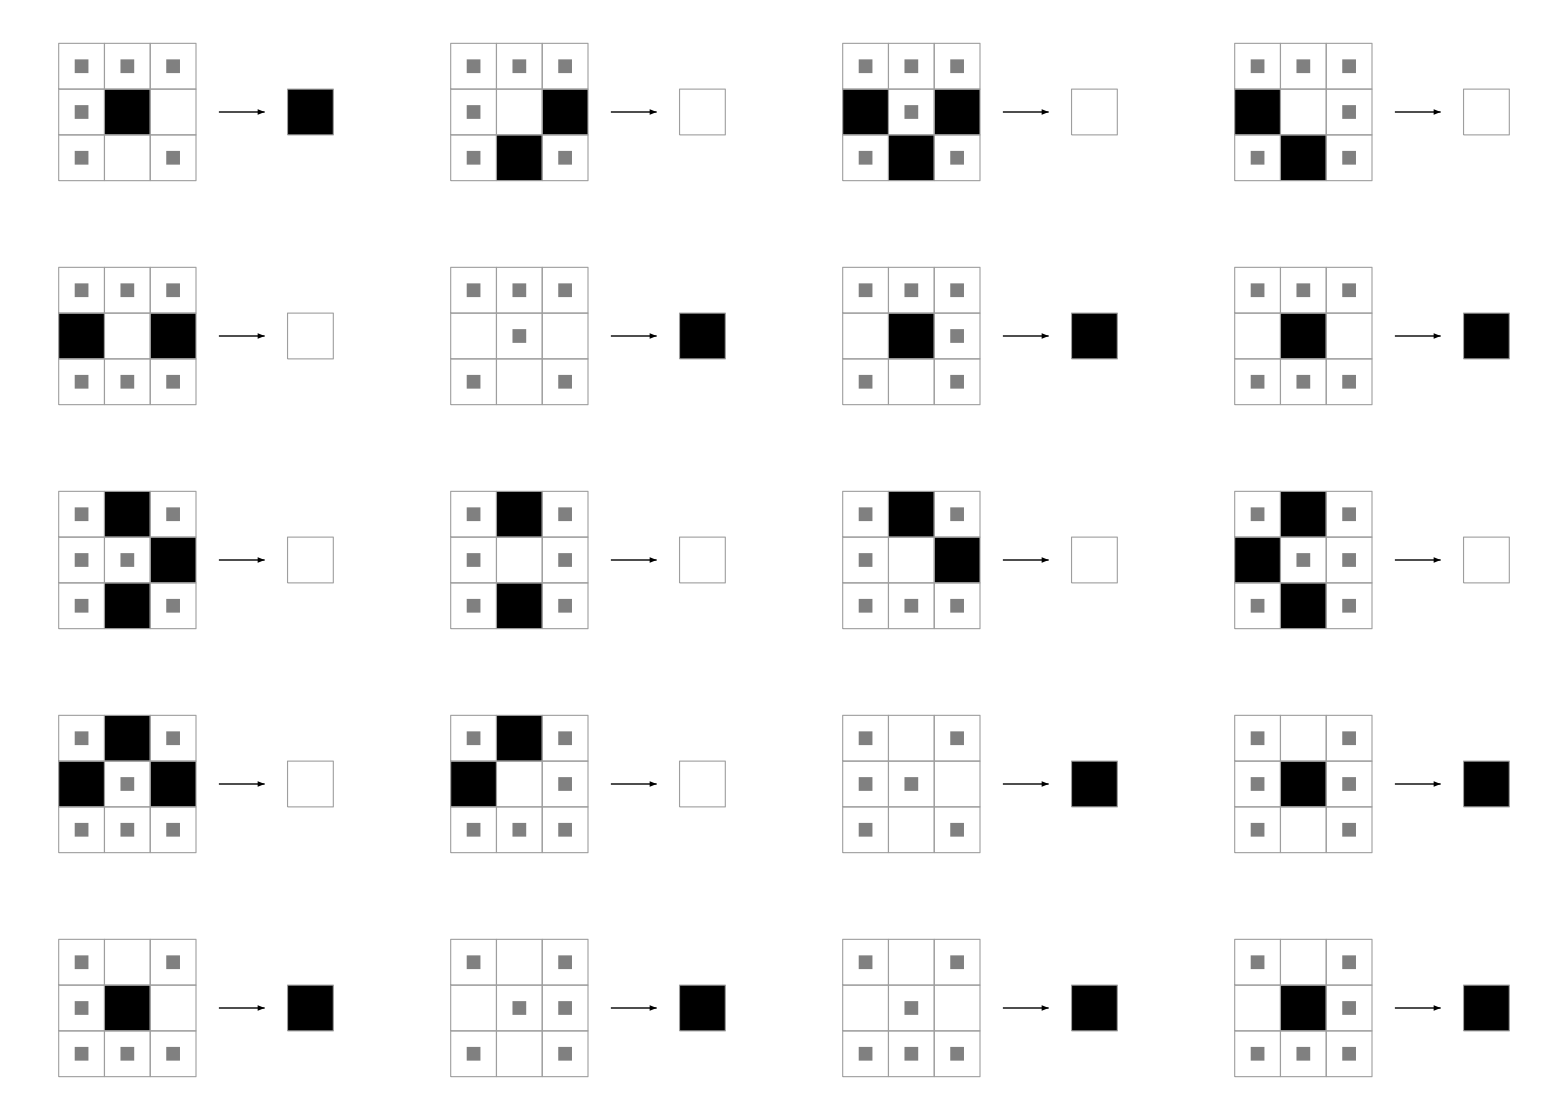

```mathematica
RulePlot[CellularAutomaton[{rulNum,2,{1,1}}],Appearance->"Simplified"]
```

## 4. Exhaustive search 3x3

```mathematica
patterns={({{0, 1, 0}, {1, 0, 1}, {0, 1, 0}}),-({{0, 1, 0}, {1, 0, 1}, {0, 1, 0}}),({{0, 1, 0}, {2, 0, 2}, {0, 1, 0}}),-({{0, 1, 0}, {2, 0, 2}, {0, 1, 0}}),({{0, 1, 0}, {-1, 0, -1}, {0, 1, 0}}),({{0, 1, 0}, {-2, 0, -2}, {0, 1, 0}}),-({{0, 1, 0}, {-2, 0, -2}, {0, 1, 0}}),({{0, 1, 0}, {0, 0, 0}, {0, 1, 0}}),-({{0, 1, 0}, {0, 0, 0}, {0, 1, 0}})};
```

```mathematica
lattice=Tuples[{0,1},{#,#}]&[3]/. 0->-1;
```

```mathematica
e[s_,patternNum_]:=Apply[Plus,s ListConvolve[patterns⟦patternNum⟧,s,2],{0,1}]
```

```mathematica
factorOutRotations[minE1_,size_] := Block[{minE = minE1, n = 1}, While[n < Length[minE],
      With[{equivalentsets = Table[RotateLeft[RotateLeft[Partition[IntegerDigits[minE[[n]], 2,size^2], size], k]ᵀ, j]ᵀ, {k, 0, size-1}, {j, 0, size-1}]},minE = Cases[minE, Except[Alternatives @@Rest@ Union@Flatten@Map[FromDigits[Flatten[#], 2] &, Join[equivalentsets,equivalentsets/.{0->1,1->0}], {2}]]]]; n++;]; minE]
```

```mathematica
exhausiveEnergies=Table[e[#,j]&/@lattice,{j,1,Length[patterns]}];
minEnergies=Min/@exhausiveEnergies
```

{-12,-36,-18,-54,-24,-42,-30,-6,-18}

```mathematica
energyMinimumPositions=MapThread[Position][{exhausiveEnergies,minEnergies}];
```

```mathematica
res4=Map[FromDigits[Flatten[lattice⟦#⟧/.-1->0],2]&,energyMinimumPositions,{3}];
```

```mathematica
groundState=factorOutRotations[#,3]&/@(Flatten[res4,{3}]⟦1⟧)
```

{{78,84,85,86,98,99,102},{0},{78,84,85,86,98,99,102},{0},{7},{7},{73},{7,14,15,28,29,30,31,78,84,85,86,98,99,102},{0,73}}

```mathematica
Row/@Map[ArrayPlot[Partition[IntegerDigits[#,2,9],3],PixelConstrained->10]&,groundState,{2}]
```

{-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-,-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-,-Graphics--Graphics-}

## 5. Exhaustive search 4x4

```mathematica
patterns={({{0, 1, 0}, {1, 0, 1}, {0, 1, 0}}),-({{0, 1, 0}, {1, 0, 1}, {0, 1, 0}}),({{0, 1, 0}, {2, 0, 2}, {0, 1, 0}}),-({{0, 1, 0}, {2, 0, 2}, {0, 1, 0}}),({{0, 1, 0}, {-1, 0, -1}, {0, 1, 0}}),({{0, 1, 0}, {-2, 0, -2}, {0, 1, 0}}),-({{0, 1, 0}, {-2, 0, -2}, {0, 1, 0}}),({{0, 1, 0}, {0, 0, 0}, {0, 1, 0}}),-({{0, 1, 0}, {0, 0, 0}, {0, 1, 0}})};
```

```mathematica
lattice4=Tuples[{0,1},{#,#}]&[4]/. 0->-1;
```

```mathematica
e[s_,patternNum_]:=Apply[Plus,s ListConvolve[patterns⟦patternNum⟧,s,2],{0,1}]
```

```mathematica
Monitor[exhausiveEnergies4=Table[e[#,j]&/@lattice4,{j,1,Length[patterns]-2}];,j]
minEnergies4=Min/@exhausiveEnergies4
```

{-64,-64,-96,-96,-64,-96,-96}

```mathematica
energyMinimumPositions4=MapThread[Position][{exhausiveEnergies4,minEnergies4}];
```

```mathematica
groundstates4=Map[ArrayPlot[lattice4⟦#⟧/.-1->0,PixelConstrained->10]&,energyMinimumPositions4,{3}]
```

({-Graphics-} | {-Graphics-}
{-Graphics-} | {-Graphics-}
{-Graphics-} | {-Graphics-}
{-Graphics-} | {-Graphics-}
{-Graphics-} | {-Graphics-}
{-Graphics-} | {-Graphics-}
{-Graphics-} | {-Graphics-})

## 6. Exhaustive search 5x5

```mathematica
energyCompiled5=Compile[{{fieldN,_Integer},{w1,_Integer},{w2,_Integer},{w3,_Integer},{w4,_Integer}},Block[{d=Partition[N[IntegerDigits[fieldN,2,25]]/. 0. ->-1.,5]},w3 (d⟦1,2⟧ d⟦2,1⟧+d⟦3,5⟧ d⟦2,1⟧+d⟦1,3⟧ d⟦2,2⟧+d⟦1,4⟧ d⟦2,3⟧+d⟦1,5⟧ d⟦2,4⟧+d⟦1,1⟧ d⟦2,5⟧+d⟦2,2⟧ d⟦3,1⟧+d⟦2,3⟧ d⟦3,2⟧+d⟦2,4⟧ d⟦3,3⟧+d⟦2,5⟧ d⟦3,4⟧+d⟦3,2⟧ d⟦4,1⟧+d⟦3,3⟧ d⟦4,2⟧+d⟦3,4⟧ d⟦4,3⟧+d⟦3,5⟧ d⟦4,4⟧+d⟦3,1⟧ d⟦4,5⟧+d⟦1,5⟧ d⟦5,1⟧+d⟦4,2⟧ d⟦5,1⟧+d⟦1,1⟧ d⟦5,2⟧+d⟦4,3⟧ d⟦5,2⟧+d⟦1,2⟧ d⟦5,3⟧+d⟦4,4⟧ d⟦5,3⟧+d⟦1,3⟧ d⟦5,4⟧+d⟦4,5⟧ d⟦5,4⟧+d⟦1,4⟧ d⟦5,5⟧+d⟦4,1⟧ d⟦5,5⟧)+w4 (d⟦1,5⟧ d⟦2,1⟧+d⟦3,2⟧ d⟦2,1⟧+d⟦1,1⟧ d⟦2,2⟧+d⟦1,2⟧ d⟦2,3⟧+d⟦1,3⟧ d⟦2,4⟧+d⟦1,4⟧ d⟦2,5⟧+d⟦2,5⟧ d⟦3,1⟧+d⟦2,2⟧ d⟦3,3⟧+d⟦2,3⟧ d⟦3,4⟧+d⟦2,4⟧ d⟦3,5⟧+d⟦3,5⟧ d⟦4,1⟧+d⟦3,1⟧ d⟦4,2⟧+d⟦3,2⟧ d⟦4,3⟧+d⟦3,3⟧ d⟦4,4⟧+d⟦3,4⟧ d⟦4,5⟧+d⟦1,2⟧ d⟦5,1⟧+d⟦4,5⟧ d⟦5,1⟧+d⟦1,3⟧ d⟦5,2⟧+d⟦4,1⟧ d⟦5,2⟧+d⟦1,4⟧ d⟦5,3⟧+d⟦4,2⟧ d⟦5,3⟧+d⟦1,5⟧ d⟦5,4⟧+d⟦4,3⟧ d⟦5,4⟧+d⟦1,1⟧ d⟦5,5⟧+d⟦4,4⟧ d⟦5,5⟧)+w1 (d⟦1,1⟧ d⟦2,1⟧+d⟦3,1⟧ d⟦2,1⟧+d⟦1,2⟧ d⟦2,2⟧+d⟦1,3⟧ d⟦2,3⟧+d⟦1,4⟧ d⟦2,4⟧+d⟦1,5⟧ d⟦2,5⟧+d⟦2,2⟧ d⟦3,2⟧+d⟦2,3⟧ d⟦3,3⟧+d⟦2,4⟧ d⟦3,4⟧+d⟦2,5⟧ d⟦3,5⟧+d⟦3,1⟧ d⟦4,1⟧+d⟦3,2⟧ d⟦4,2⟧+d⟦3,3⟧ d⟦4,3⟧+d⟦3,4⟧ d⟦4,4⟧+d⟦3,5⟧ d⟦4,5⟧+d⟦1,1⟧ d⟦5,1⟧+d⟦4,1⟧ d⟦5,1⟧+d⟦1,2⟧ d⟦5,2⟧+d⟦4,2⟧ d⟦5,2⟧+d⟦1,3⟧ d⟦5,3⟧+d⟦4,3⟧ d⟦5,3⟧+d⟦1,4⟧ d⟦5,4⟧+d⟦4,4⟧ d⟦5,4⟧+d⟦1,5⟧ d⟦5,5⟧+d⟦4,5⟧ d⟦5,5⟧)+w2 (d⟦1,1⟧ d⟦1,2⟧+d⟦1,3⟧ d⟦1,2⟧+d⟦1,3⟧ d⟦1,4⟧+d⟦1,1⟧ d⟦1,5⟧+d⟦1,4⟧ d⟦1,5⟧+d⟦2,1⟧ d⟦2,2⟧+d⟦2,2⟧ d⟦2,3⟧+d⟦2,3⟧ d⟦2,4⟧+d⟦2,1⟧ d⟦2,5⟧+d⟦2,4⟧ d⟦2,5⟧+d⟦3,1⟧ d⟦3,2⟧+d⟦3,2⟧ d⟦3,3⟧+d⟦3,3⟧ d⟦3,4⟧+d⟦3,1⟧ d⟦3,5⟧+d⟦3,4⟧ d⟦3,5⟧+d⟦4,1⟧ d⟦4,2⟧+d⟦4,2⟧ d⟦4,3⟧+d⟦4,3⟧ d⟦4,4⟧+d⟦4,1⟧ d⟦4,5⟧+d⟦4,4⟧ d⟦4,5⟧+d⟦5,1⟧ d⟦5,2⟧+d⟦5,2⟧ d⟦5,3⟧+d⟦5,3⟧ d⟦5,4⟧+d⟦5,1⟧ d⟦5,5⟧+d⟦5,4⟧ d⟦5,5⟧)],CompilationTarget->"C",CompilationOptions->{"InlineExternalDefinitions"->True},
RuntimeAttributes->{Listable},Parallelization->True]
```

CompiledFunction[…]

```mathematica
factorOutRotations[minE1_,size_] := Block[{minE = minE1, n = 1}, While[n < Length[minE],
      With[{equivalentsets = Table[RotateLeft[RotateLeft[Partition[IntegerDigits[minE[[n]], 2,size^2], size], k]ᵀ, j]ᵀ, {k, 0, size-1}, {j, 0, size-1}]},minE = Cases[minE, Except[Alternatives @@Rest@ Union@Flatten@Map[FromDigits[Flatten[#], 2] &, Join[equivalentsets,equivalentsets/.{0->1,1->0}], {2}]]]]; n++;]; minE]
```

```mathematica
res=Table[If[w2 w1≠0,{w1,w2,0,0}->factorOutRotations[Flatten[Position[#,Min[#]]-1],5]&[ParallelMap[energyCompiled5[#,w1,w2,0,0]&,Range[0,2^25-1],{1}]]],{w1,-2,2},{w2,-2,2}]
```

({-2,-2,0,0}→{0} | {-2,-1,0,0}→{0} | Null | {-2,1,0,0}→{5412005} | {-2,2,0,0}→{5412005}
{-1,-2,0,0}→{0} | {-1,-1,0,0}→{0} | Null | {-1,1,0,0}→{5412005} | {-1,2,0,0}→{5412005}
Null | Null | Null | Null | Null
{1,-2,0,0}→{31775} | {1,-1,0,0}→{31775} | Null | {1,1,0,0}→{5433530,5556410,5556658,5556666,5560506,5560626,5560630,5560634,5560754,5560762,5564602,5591346,5591350,5591354,5591414,5591482,5592250,5592374,5592378,5592405,5592406,5592410,5593274,5593398,5593402,5597370,5842106,5842570,5842571,5842586,5842618,5842633,5842635,5842650,5843130,5843642,5844154,5844619,5844634,5846202,5846603,5846605,5846618,5846667,5846682,5846714,5859514,5909690,5910155,5910170,5925050} | {1,2,0,0}→{5433530,5556410,5556658,5556666,5560506,5560626,5560630,5560634,5560754,5560762,5564602,5591346,5591350,5591354,5591414,5591482,5592250,5592374,5592378,5592405,5592406,5592410,5593274,5593398,5593402,5597370,5842106,5842570,5842571,5842586,5842618,5842633,5842635,5842650,5843130,5843642,5844154,5844619,5844634,5846202,5846603,5846605,5846618,5846667,5846682,5846714,5859514,5909690,5910155,5910170,5925050}
{2,-2,0,0}→{31775} | {2,-1,0,0}→{31775} | Null | {2,1,0,0}→{5433530,5556410,5556658,5556666,5560506,5560626,5560630,5560634,5560754,5560762,5564602,5591346,5591350,5591354,5591414,5591482,5592250,5592374,5592378,5592405,5592406,5592410,5593274,5593398,5593402,5597370,5842106,5842570,5842571,5842586,5842618,5842633,5842635,5842650,5843130,5843642,5844154,5844619,5844634,5846202,5846603,5846605,5846618,5846667,5846682,5846714,5859514,5909690,5910155,5910170,5925050} | {2,2,0,0}→{5433530,5556410,5556658,5556666,5560506,5560626,5560630,5560634,5560754,5560762,5564602,5591346,5591350,5591354,5591414,5591482,5592250,5592374,5592378,5592405,5592406,5592410,5593274,5593398,5593402,5597370,5842106,5842570,5842571,5842586,5842618,5842633,5842635,5842650,5843130,5843642,5844154,5844619,5844634,5846202,5846603,5846605,5846618,5846667,5846682,5846714,5859514,5909690,5910155,5910170,5925050})

```mathematica
res1=Column@DeleteCases[Flatten@res,Null]/.(a_->b_):>a->Row[ (ArrayPlot[Partition[IntegerDigits[#,2,25],5],PixelConstrained->10]&/@b)]
```

{-2,-2,0,0}→-Graphics-
{-2,-1,0,0}→-Graphics-
{-2,1,0,0}→-Graphics-
{-2,2,0,0}→-Graphics-
{-1,-2,0,0}→-Graphics-
{-1,-1,0,0}→-Graphics-
{-1,1,0,0}→-Graphics-
{-1,2,0,0}→-Graphics-
{1,-2,0,0}→-Graphics-
{1,-1,0,0}→-Graphics-
{1,1,0,0}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{1,2,0,0}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{2,-2,0,0}→-Graphics-
{2,-1,0,0}→-Graphics-
{2,1,0,0}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{2,2,0,0}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
E5=energyCompiled5[5433530,4,2,0,0]/25
```

-3.6

## 7. Exhaustive search 6x6

```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
energyCompiled6=Compile[{{fieldN,_Integer},{w1,_Integer},{w2,_Integer},{w3,_Integer},{w4,_Integer}},
Block[{d=Partition[N[IntegerDigits[fieldN,2,36]]/. 0. ->-1.,6]}, w3 (d⟦1,2⟧ d⟦2,1⟧+d⟦3,6⟧ d⟦2,1⟧+d⟦1,3⟧ d⟦2,2⟧+d⟦1,4⟧ d⟦2,3⟧+d⟦1,5⟧ d⟦2,4⟧+d⟦1,6⟧ d⟦2,5⟧+d⟦1,1⟧ d⟦2,6⟧+d⟦2,2⟧ d⟦3,1⟧+d⟦2,3⟧ d⟦3,2⟧+d⟦2,4⟧ d⟦3,3⟧+d⟦2,5⟧ d⟦3,4⟧+d⟦2,6⟧ d⟦3,5⟧+d⟦3,2⟧ d⟦4,1⟧+d⟦3,3⟧ d⟦4,2⟧+d⟦3,4⟧ d⟦4,3⟧+d⟦3,5⟧ d⟦4,4⟧+d⟦3,6⟧ d⟦4,5⟧+d⟦3,1⟧ d⟦4,6⟧+d⟦4,2⟧ d⟦5,1⟧+d⟦4,3⟧ d⟦5,2⟧+d⟦4,4⟧ d⟦5,3⟧+d⟦4,5⟧ d⟦5,4⟧+d⟦4,6⟧ d⟦5,5⟧+d⟦4,1⟧ d⟦5,6⟧+d⟦1,6⟧ d⟦6,1⟧+d⟦5,2⟧ d⟦6,1⟧+d⟦1,1⟧ d⟦6,2⟧+d⟦5,3⟧ d⟦6,2⟧+d⟦1,2⟧ d⟦6,3⟧+d⟦5,4⟧ d⟦6,3⟧+d⟦1,3⟧ d⟦6,4⟧+d⟦5,5⟧ d⟦6,4⟧+d⟦1,4⟧ d⟦6,5⟧+d⟦5,6⟧ d⟦6,5⟧+d⟦1,5⟧ d⟦6,6⟧+d⟦5,1⟧ d⟦6,6⟧)
+w4 (d⟦1,6⟧ d⟦2,1⟧+d⟦3,2⟧ d⟦2,1⟧+d⟦1,1⟧ d⟦2,2⟧+d⟦1,2⟧ d⟦2,3⟧+d⟦1,3⟧ d⟦2,4⟧+d⟦1,4⟧ d⟦2,5⟧+d⟦1,5⟧ d⟦2,6⟧+d⟦2,6⟧ d⟦3,1⟧+d⟦2,2⟧ d⟦3,3⟧+d⟦2,3⟧ d⟦3,4⟧+d⟦2,4⟧ d⟦3,5⟧+d⟦2,5⟧ d⟦3,6⟧+d⟦3,6⟧ d⟦4,1⟧+d⟦3,1⟧ d⟦4,2⟧+d⟦3,2⟧ d⟦4,3⟧+d⟦3,3⟧ d⟦4,4⟧+d⟦3,4⟧ d⟦4,5⟧+d⟦3,5⟧ d⟦4,6⟧+d⟦4,6⟧ d⟦5,1⟧+d⟦4,1⟧ d⟦5,2⟧+d⟦4,2⟧ d⟦5,3⟧+d⟦4,3⟧ d⟦5,4⟧+d⟦4,4⟧ d⟦5,5⟧+d⟦4,5⟧ d⟦5,6⟧+d⟦1,2⟧ d⟦6,1⟧+d⟦5,6⟧ d⟦6,1⟧+d⟦1,3⟧ d⟦6,2⟧+d⟦5,1⟧ d⟦6,2⟧+d⟦1,4⟧ d⟦6,3⟧+d⟦5,2⟧ d⟦6,3⟧+d⟦1,5⟧ d⟦6,4⟧+d⟦5,3⟧ d⟦6,4⟧+d⟦1,6⟧ d⟦6,5⟧+d⟦5,4⟧ d⟦6,5⟧+d⟦1,1⟧ d⟦6,6⟧+d⟦5,5⟧ d⟦6,6⟧)
+w1 (d⟦1,1⟧ d⟦2,1⟧+d⟦3,1⟧ d⟦2,1⟧+d⟦1,2⟧ d⟦2,2⟧+d⟦1,3⟧ d⟦2,3⟧+d⟦1,4⟧ d⟦2,4⟧+d⟦1,5⟧ d⟦2,5⟧+d⟦1,6⟧ d⟦2,6⟧+d⟦2,2⟧ d⟦3,2⟧+d⟦2,3⟧ d⟦3,3⟧+d⟦2,4⟧ d⟦3,4⟧+d⟦2,5⟧ d⟦3,5⟧+d⟦2,6⟧ d⟦3,6⟧+d⟦3,1⟧ d⟦4,1⟧+d⟦3,2⟧ d⟦4,2⟧+d⟦3,3⟧ d⟦4,3⟧+d⟦3,4⟧ d⟦4,4⟧+d⟦3,5⟧ d⟦4,5⟧+d⟦3,6⟧ d⟦4,6⟧+d⟦4,1⟧ d⟦5,1⟧+d⟦4,2⟧ d⟦5,2⟧+d⟦4,3⟧ d⟦5,3⟧+d⟦4,4⟧ d⟦5,4⟧+d⟦4,5⟧ d⟦5,5⟧+d⟦4,6⟧ d⟦5,6⟧+d⟦1,1⟧ d⟦6,1⟧+d⟦5,1⟧ d⟦6,1⟧+d⟦1,2⟧ d⟦6,2⟧+d⟦5,2⟧ d⟦6,2⟧+d⟦1,3⟧ d⟦6,3⟧+d⟦5,3⟧ d⟦6,3⟧+d⟦1,4⟧ d⟦6,4⟧+d⟦5,4⟧ d⟦6,4⟧+d⟦1,5⟧ d⟦6,5⟧+d⟦5,5⟧ d⟦6,5⟧+d⟦1,6⟧ d⟦6,6⟧+d⟦5,6⟧ d⟦6,6⟧)
+w2 (d⟦1,1⟧ d⟦1,2⟧+d⟦1,3⟧ d⟦1,2⟧+d⟦1,3⟧ d⟦1,4⟧+d⟦1,4⟧ d⟦1,5⟧+d⟦1,1⟧ d⟦1,6⟧+d⟦1,5⟧ d⟦1,6⟧+d⟦2,1⟧ d⟦2,2⟧+d⟦2,2⟧ d⟦2,3⟧+d⟦2,3⟧ d⟦2,4⟧+d⟦2,4⟧ d⟦2,5⟧+d⟦2,1⟧ d⟦2,6⟧+d⟦2,5⟧ d⟦2,6⟧+d⟦3,1⟧ d⟦3,2⟧+d⟦3,2⟧ d⟦3,3⟧+d⟦3,3⟧ d⟦3,4⟧+d⟦3,4⟧ d⟦3,5⟧+d⟦3,1⟧ d⟦3,6⟧+d⟦3,5⟧ d⟦3,6⟧+d⟦4,1⟧ d⟦4,2⟧+d⟦4,2⟧ d⟦4,3⟧+d⟦4,3⟧ d⟦4,4⟧+d⟦4,4⟧ d⟦4,5⟧+d⟦4,1⟧ d⟦4,6⟧+d⟦4,5⟧ d⟦4,6⟧+d⟦5,1⟧ d⟦5,2⟧+d⟦5,2⟧ d⟦5,3⟧+d⟦5,3⟧ d⟦5,4⟧+d⟦5,4⟧ d⟦5,5⟧+d⟦5,1⟧ d⟦5,6⟧+d⟦5,5⟧ d⟦5,6⟧+d⟦6,1⟧ d⟦6,2⟧+d⟦6,2⟧ d⟦6,3⟧+d⟦6,3⟧ d⟦6,4⟧+d⟦6,4⟧ d⟦6,5⟧+d⟦6,1⟧ d⟦6,6⟧+d⟦6,5⟧ d⟦6,6⟧)],
CompilationTarget->"C",CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->True},RuntimeAttributes->{Listable},Parallelization->True]
```

CompiledFunction[…]

```mathematica
minenergy={{0},energyCompiled6[0,4,2,4,-2]};
findMinEnergyCompiledFully[step_,w1_,w2_,w3_,w4_]:=Block[{field,currentEnergy,t},
Do[t=AbsoluteTiming[field=ParallelMap[energyCompiled6[#,w1,w2,w3,w4]&,Range[step*(n-1),step*n-1],{1}];currentEnergy=Min[field];
If[currentEnergy<=minenergy⟦2⟧,If[currentEnergy==minenergy⟦2⟧,minenergy⟦1⟧=Join[minenergy⟦1⟧,Flatten[Position[field,currentEnergy]-1+step*(n-1)]];,
minenergy={Flatten[Position[field,currentEnergy]-1+step*(n-1)],currentEnergy};];minenergy>>"minenergy"]];
Print[Row@{"Time taken ",t⟦1⟧/60," min.,   step = ",n,"/",2^36/step",  Emin = ",minenergy⟦2⟧,",  # states =",Length[minenergy⟦1⟧]}],{n,1,2^36/step}]]
```

```mathematica
factorOutRotations[minE1_]:=Block[{minE=minE1,n=1},While[n<Length[minE],
With[{equivalentsets=Table[RotateLeft[RotateLeft[Partition[IntegerDigits[minE⟦n⟧,2,36],6],k]ᵀ,j]ᵀ,{k,0,5},{j,0,5}]},
minE=Cases[minE,Except[Alternatives@@Rest@Union@Flatten@Map[FromDigits[Flatten[#],2]&,equivalentsets,{2}]]]];n++;];minE]
```

```mathematica
findMinEnergyCompiledFully[2^27,4,2,4,-2]
```

```mathematica
minenergy1=factorOutRotations[minenergy⟦1⟧]
Length[minenergy1]
ArrayPlot[Partition[N[IntegerDigits[#,2,36]],6],PixelConstrained->5]&/@Take[minenergy1,UpTo[100]]
```

```mathematica
E6=energyCompiled6[FromDigits[Flatten@({{1, 0, 1, 0, 1, 0}, {0, 1, 0, 1, 0, 1}, {1, 0, 1, 0, 1, 0}, {0, 1, 0, 1, 0, 1}, {1, 0, 1, 0, 1, 0}, {0, 1, 0, 1, 0, 1}}),2],4,2,0,0]/36
ArrayPlot[({{1, 0, 1, 0, 1, 0}, {0, 1, 0, 1, 0, 1}, {1, 0, 1, 0, 1, 0}, {0, 1, 0, 1, 0, 1}, {1, 0, 1, 0, 1, 0}, {0, 1, 0, 1, 0, 1}}),PixelConstrained->10]
```

-6.

-Graphics-

## 8. Comparison of exact ground state for 4x4 and MonteCarlo for 64x64

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\grabovsk\Google Drive\Works\Mathematica_Problems\Final_Project\Final-Project

```mathematica
energyCompiled4=Compile[{{fieldN,_Integer},{w1,_Integer},{w2,_Integer},{w3,_Integer},{w4,_Integer}},
Block[{d=Partition[N[IntegerDigits[fieldN,2,16]]/. 0. ->-1.,4]}, w1 (d⟦1,1⟧ d⟦2,1⟧+d⟦3,1⟧ d⟦2,1⟧+d⟦1,2⟧ d⟦2,2⟧+d⟦1,3⟧ d⟦2,3⟧+d⟦1,4⟧ d⟦2,4⟧+d⟦2,2⟧ d⟦3,2⟧+d⟦2,3⟧ d⟦3,3⟧+d⟦2,4⟧ d⟦3,4⟧+d⟦1,1⟧ d⟦4,1⟧+d⟦3,1⟧ d⟦4,1⟧+d⟦1,2⟧ d⟦4,2⟧+d⟦3,2⟧ d⟦4,2⟧+d⟦1,3⟧ d⟦4,3⟧+d⟦3,3⟧ d⟦4,3⟧+d⟦1,4⟧ d⟦4,4⟧+d⟦3,4⟧ d⟦4,4⟧)+w2 (d⟦1,1⟧ d⟦1,2⟧+d⟦1,3⟧ d⟦1,2⟧+d⟦1,1⟧ d⟦1,4⟧+d⟦1,3⟧ d⟦1,4⟧+d⟦2,1⟧ d⟦2,2⟧+d⟦2,2⟧ d⟦2,3⟧+d⟦2,1⟧ d⟦2,4⟧+d⟦2,3⟧ d⟦2,4⟧+d⟦3,1⟧ d⟦3,2⟧+d⟦3,2⟧ d⟦3,3⟧+d⟦3,1⟧ d⟦3,4⟧+d⟦3,3⟧ d⟦3,4⟧+d⟦4,1⟧ d⟦4,2⟧+d⟦4,2⟧ d⟦4,3⟧+d⟦4,1⟧ d⟦4,4⟧+d⟦4,3⟧ d⟦4,4⟧)+w3 (d⟦1,2⟧ d⟦2,1⟧+d⟦3,4⟧ d⟦2,1⟧+d⟦1,3⟧ d⟦2,2⟧+d⟦1,4⟧ d⟦2,3⟧+d⟦1,1⟧ d⟦2,4⟧+d⟦2,2⟧ d⟦3,1⟧+d⟦2,3⟧ d⟦3,2⟧+d⟦2,4⟧ d⟦3,3⟧+d⟦1,4⟧ d⟦4,1⟧+d⟦3,2⟧ d⟦4,1⟧+d⟦1,1⟧ d⟦4,2⟧+d⟦3,3⟧ d⟦4,2⟧+d⟦1,2⟧ d⟦4,3⟧+d⟦3,4⟧ d⟦4,3⟧+d⟦1,3⟧ d⟦4,4⟧+d⟦3,1⟧ d⟦4,4⟧)+w4 (d⟦1,4⟧ d⟦2,1⟧+d⟦3,2⟧ d⟦2,1⟧+d⟦1,1⟧ d⟦2,2⟧+d⟦1,2⟧ d⟦2,3⟧+d⟦1,3⟧ d⟦2,4⟧+d⟦2,4⟧ d⟦3,1⟧+d⟦2,2⟧ d⟦3,3⟧+d⟦2,3⟧ d⟦3,4⟧+d⟦1,2⟧ d⟦4,1⟧+d⟦3,4⟧ d⟦4,1⟧+d⟦1,3⟧ d⟦4,2⟧+d⟦3,1⟧ d⟦4,2⟧+d⟦1,4⟧ d⟦4,3⟧+d⟦3,2⟧ d⟦4,3⟧+d⟦1,1⟧ d⟦4,4⟧+d⟦3,3⟧ d⟦4,4⟧)],
CompilationTarget->"C",CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->True},RuntimeAttributes->{Listable},Parallelization->True]
```

CompiledFunction[…]

```mathematica
factorOutRotations[minE1_,size_] := Block[{minE = minE1, n = 1}, While[n < Length[minE],With[{equivalentsets = Table[RotateLeft[RotateLeft[Partition[IntegerDigits[minE[[n]], 2,size^2], size], k]ᵀ, j]ᵀ, {k, 0, size-1}, {j, 0, size-1}]},minE = Cases[minE, Except[Alternatives @@Rest@ Union@Flatten@Map[FromDigits[Flatten[#], 2] &, Join[equivalentsets,equivalentsets/.{0->1,1->0}], {2}]]]]; n++;]; minE]
```

```mathematica
res44=Table[Print[{w1,w2,w3,w4}];If[w1==w2==w3==w4==0,{0,0,0,0}->0,{w1,w2,w3,w4}->factorOutRotations[Flatten[Position[#,Min[#]]-1],4]&[ParallelMap[energyCompiled4[#,w1,w2,w3,w4]&,Range[0,2^16-1],{1}]]],{w1,-2,2},{w2,-2,2},{w3,-2,2},{w4,-2,2}];
```

```mathematica
res45=Flatten[res44/.(a_->b_):>a->Row[(ArrayPlot[Partition[IntegerDigits[#,2,16],4],PixelConstrained->10]&/@b),Spacer[20]]];
```

```mathematica
res455=Column/@Partition[res45,25]
```

{{-2,-2,-2,-2}→-Graphics-
{-2,-2,-2,-1}→-Graphics-
{-2,-2,-2,0}→-Graphics-
{-2,-2,-2,1}→-Graphics-
{-2,-2,-2,2}→-Graphics--Graphics-
{-2,-2,-1,-2}→-Graphics-
{-2,-2,-1,-1}→-Graphics-
{-2,-2,-1,0}→-Graphics-
{-2,-2,-1,1}→-Graphics-
{-2,-2,-1,2}→-Graphics--Graphics-
{-2,-2,0,-2}→-Graphics-
{-2,-2,0,-1}→-Graphics-
{-2,-2,0,0}→-Graphics-
{-2,-2,0,1}→-Graphics-
{-2,-2,0,2}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{-2,-2,1,-2}→-Graphics-
{-2,-2,1,-1}→-Graphics-
{-2,-2,1,0}→-Graphics-
{-2,-2,1,1}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{-2,-2,1,2}→-Graphics--Graphics-
{-2,-2,2,-2}→-Graphics--Graphics-
{-2,-2,2,-1}→-Graphics--Graphics-
{-2,-2,2,0}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{-2,-2,2,1}→-Graphics--Graphics-
{-2,-2,2,2}→-Graphics--Graphics-,{-2,-1,-2,-2}→-Graphics-
{-2,-1,-2,-1}→-Graphics-
{-2,-1,-2,0}→-Graphics-
{-2,-1,-2,1}→-Graphics-
{-2,-1,-2,2}→-Graphics-
{-2,-1,-1,-2}→-Graphics-
{-2,-1,-1,-1}→-Graphics-
{-2,-1,-1,0}→-Graphics-
{-2,-1,-1,1}→-Graphics-
{-2,-1,-1,2}→-Graphics-
{-2,-1,0,-2}→-Graphics-
{-2,-1,0,-1}→-Graphics-
{-2,-1,0,0}→-Graphics-
{-2,-1,0,1}→-Graphics--Graphics--Graphics--Graphics-
{-2,-1,0,2}→-Graphics-
{-2,-1,1,-2}→-Graphics-
{-2,-1,1,-1}→-Graphics-
{-2,-1,1,0}→-Graphics--Graphics--Graphics--Graphics-
{-2,-1,1,1}→-Graphics-
{-2,-1,1,2}→-Graphics-
{-2,-1,2,-2}→-Graphics-
{-2,-1,2,-1}→-Graphics-
{-2,-1,2,0}→-Graphics-
{-2,-1,2,1}→-Graphics-
{-2,-1,2,2}→-Graphics-,{-2,0,-2,-2}→-Graphics-
{-2,0,-2,-1}→-Graphics-
{-2,0,-2,0}→-Graphics-
{-2,0,-2,1}→-Graphics--Graphics-
{-2,0,-2,2}→-Graphics-
{-2,0,-1,-2}→-Graphics-
{-2,0,-1,-1}→-Graphics-
{-2,0,-1,0}→-Graphics-
{-2,0,-1,1}→-Graphics--Graphics--Graphics--Graphics--Graphics-
{-2,0,-1,2}→-Graphics--Graphics-
{-2,0,0,-2}→-Graphics-
{-2,0,0,-1}→-Graphics-
{-2,0,0,0}→-Graphics--Graphics--Graphics--Graphics-
{-2,0,0,1}→-Graphics-
{-2,0,0,2}→-Graphics-
{-2,0,1,-2}→-Graphics--Graphics-
{-2,0,1,-1}→-Graphics--Graphics--Graphics--Graphics--Graphics-
{-2,0,1,0}→-Graphics-
{-2,0,1,1}→-Graphics-
{-2,0,1,2}→-Graphics-
{-2,0,2,-2}→-Graphics-
{-2,0,2,-1}→-Graphics--Graphics-
{-2,0,2,0}→-Graphics-
{-2,0,2,1}→-Graphics-
{-2,0,2,2}→-Graphics-,{-2,1,-2,-2}→-Graphics-
{-2,1,-2,-1}→-Graphics-
{-2,1,-2,0}→-Graphics-
{-2,1,-2,1}→-Graphics-
{-2,1,-2,2}→-Graphics-
{-2,1,-1,-2}→-Graphics-
{-2,1,-1,-1}→-Graphics-
{-2,1,-1,0}→-Graphics--Graphics--Graphics--Graphics-
{-2,1,-1,1}→-Graphics-
{-2,1,-1,2}→-Graphics-
{-2,1,0,-2}→-Graphics-
{-2,1,0,-1}→-Graphics--Graphics--Graphics--Graphics-
{-2,1,0,0}→-Graphics-
{-2,1,0,1}→-Graphics-
{-2,1,0,2}→-Graphics-
{-2,1,1,-2}→-Graphics-
{-2,1,1,-1}→-Graphics-
{-2,1,1,0}→-Graphics-
{-2,1,1,1}→-Graphics-
{-2,1,1,2}→-Graphics-
{-2,1,2,-2}→-Graphics-
{-2,1,2,-1}→-Graphics-
{-2,1,2,0}→-Graphics-
{-2,1,2,1}→-Graphics-
{-2,1,2,2}→-Graphics-,{-2,2,-2,-2}→-Graphics--Graphics-
{-2,2,-2,-1}→-Graphics--Graphics-
{-2,2,-2,0}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{-2,2,-2,1}→-Graphics--Graphics-
{-2,2,-2,2}→-Graphics--Graphics-
{-2,2,-1,-2}→-Graphics--Graphics-
{-2,2,-1,-1}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{-2,2,-1,0}→-Graphics-
{-2,2,-1,1}→-Graphics-
{-2,2,-1,2}→-Graphics-
{-2,2,0,-2}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{-2,2,0,-1}→-Graphics-
{-2,2,0,0}→-Graphics-
{-2,2,0,1}→-Graphics-
{-2,2,0,2}→-Graphics-
{-2,2,1,-2}→-Graphics--Graphics-
{-2,2,1,-1}→-Graphics-
{-2,2,1,0}→-Graphics-
{-2,2,1,1}→-Graphics-
{-2,2,1,2}→-Graphics-
{-2,2,2,-2}→-Graphics--Graphics-
{-2,2,2,-1}→-Graphics-
{-2,2,2,0}→-Graphics-
{-2,2,2,1}→-Graphics-
{-2,2,2,2}→-Graphics-,{-1,-2,-2,-2}→-Graphics-
{-1,-2,-2,-1}→-Graphics-
{-1,-2,-2,0}→-Graphics-
{-1,-2,-2,1}→-Graphics-
{-1,-2,-2,2}→-Graphics-
{-1,-2,-1,-2}→-Graphics-
{-1,-2,-1,-1}→-Graphics-
{-1,-2,-1,0}→-Graphics-
{-1,-2,-1,1}→-Graphics-
{-1,-2,-1,2}→-Graphics-
{-1,-2,0,-2}→-Graphics-
{-1,-2,0,-1}→-Graphics-
{-1,-2,0,0}→-Graphics-
{-1,-2,0,1}→-Graphics--Graphics--Graphics--Graphics-
{-1,-2,0,2}→-Graphics-
{-1,-2,1,-2}→-Graphics-
{-1,-2,1,-1}→-Graphics-
{-1,-2,1,0}→-Graphics--Graphics--Graphics--Graphics-
{-1,-2,1,1}→-Graphics-
{-1,-2,1,2}→-Graphics-
{-1,-2,2,-2}→-Graphics-
{-1,-2,2,-1}→-Graphics-
{-1,-2,2,0}→-Graphics-
{-1,-2,2,1}→-Graphics-
{-1,-2,2,2}→-Graphics-,{-1,-1,-2,-2}→-Graphics-
{-1,-1,-2,-1}→-Graphics-
{-1,-1,-2,0}→-Graphics-
{-1,-1,-2,1}→-Graphics--Graphics-
{-1,-1,-2,2}→-Graphics-
{-1,-1,-1,-2}→-Graphics-
{-1,-1,-1,-1}→-Graphics-
{-1,-1,-1,0}→-Graphics-
{-1,-1,-1,1}→-Graphics--Graphics-
{-1,-1,-1,2}→-Graphics-
{-1,-1,0,-2}→-Graphics-
{-1,-1,0,-1}→-Graphics-
{-1,-1,0,0}→-Graphics-
{-1,-1,0,1}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{-1,-1,0,2}→-Graphics--Graphics--Graphics--Graphics-
{-1,-1,1,-2}→-Graphics--Graphics-
{-1,-1,1,-1}→-Graphics--Graphics-
{-1,-1,1,0}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{-1,-1,1,1}→-Graphics--Graphics-
{-1,-1,1,2}→-Graphics--Graphics-
{-1,-1,2,-2}→-Graphics-
{-1,-1,2,-1}→-Graphics-
{-1,-1,2,0}→-Graphics--Graphics--Graphics--Graphics-
{-1,-1,2,1}→-Graphics--Graphics-
{-1,-1,2,2}→-Graphics--Graphics-,{-1,0,-2,-2}→-Graphics-
{-1,0,-2,-1}→-Graphics-
{-1,0,-2,0}→-Graphics-
{-1,0,-2,1}→-Graphics-
{-1,0,-2,2}→-Graphics-
{-1,0,-1,-2}→-Graphics-
{-1,0,-1,-1}→-Graphics-
{-1,0,-1,0}→-Graphics-
{-1,0,-1,1}→-Graphics-
{-1,0,-1,2}→-Graphics-
{-1,0,0,-2}→-Graphics-
{-1,0,0,-1}→-Graphics-
{-1,0,0,0}→-Graphics--Graphics--Graphics--Graphics-
{-1,0,0,1}→-Graphics-
{-1,0,0,2}→-Graphics-
{-1,0,1,-2}→-Graphics-
{-1,0,1,-1}→-Graphics-
{-1,0,1,0}→-Graphics-
{-1,0,1,1}→-Graphics-
{-1,0,1,2}→-Graphics-
{-1,0,2,-2}→-Graphics-
{-1,0,2,-1}→-Graphics-
{-1,0,2,0}→-Graphics-
{-1,0,2,1}→-Graphics-
{-1,0,2,2}→-Graphics-,{-1,1,-2,-2}→-Graphics--Graphics-
{-1,1,-2,-1}→-Graphics--Graphics-
{-1,1,-2,0}→-Graphics--Graphics--Graphics--Graphics-
{-1,1,-2,1}→-Graphics-
{-1,1,-2,2}→-Graphics-
{-1,1,-1,-2}→-Graphics--Graphics-
{-1,1,-1,-1}→-Graphics--Graphics-
{-1,1,-1,0}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{-1,1,-1,1}→-Graphics--Graphics-
{-1,1,-1,2}→-Graphics--Graphics-
{-1,1,0,-2}→-Graphics--Graphics--Graphics--Graphics-
{-1,1,0,-1}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{-1,1,0,0}→-Graphics-
{-1,1,0,1}→-Graphics-
{-1,1,0,2}→-Graphics-
{-1,1,1,-2}→-Graphics-
{-1,1,1,-1}→-Graphics--Graphics-
{-1,1,1,0}→-Graphics-
{-1,1,1,1}→-Graphics-
{-1,1,1,2}→-Graphics-
{-1,1,2,-2}→-Graphics-
{-1,1,2,-1}→-Graphics--Graphics-
{-1,1,2,0}→-Graphics-
{-1,1,2,1}→-Graphics-
{-1,1,2,2}→-Graphics-,{-1,2,-2,-2}→-Graphics-
{-1,2,-2,-1}→-Graphics-
{-1,2,-2,0}→-Graphics-
{-1,2,-2,1}→-Graphics-
{-1,2,-2,2}→-Graphics-
{-1,2,-1,-2}→-Graphics-
{-1,2,-1,-1}→-Graphics-
{-1,2,-1,0}→-Graphics--Graphics--Graphics--Graphics-
{-1,2,-1,1}→-Graphics-
{-1,2,-1,2}→-Graphics-
{-1,2,0,-2}→-Graphics-
{-1,2,0,-1}→-Graphics--Graphics--Graphics--Graphics-
{-1,2,0,0}→-Graphics-
{-1,2,0,1}→-Graphics-
{-1,2,0,2}→-Graphics-
{-1,2,1,-2}→-Graphics-
{-1,2,1,-1}→-Graphics-
{-1,2,1,0}→-Graphics-
{-1,2,1,1}→-Graphics-
{-1,2,1,2}→-Graphics-
{-1,2,2,-2}→-Graphics-
{-1,2,2,-1}→-Graphics-
{-1,2,2,0}→-Graphics-
{-1,2,2,1}→-Graphics-
{-1,2,2,2}→-Graphics-,{0,-2,-2,-2}→-Graphics-
{0,-2,-2,-1}→-Graphics-
{0,-2,-2,0}→-Graphics-
{0,-2,-2,1}→-Graphics--Graphics-
{0,-2,-2,2}→-Graphics-
{0,-2,-1,-2}→-Graphics-
{0,-2,-1,-1}→-Graphics-
{0,-2,-1,0}→-Graphics-
{0,-2,-1,1}→-Graphics--Graphics--Graphics--Graphics--Graphics-
{0,-2,-1,2}→-Graphics--Graphics-
{0,-2,0,-2}→-Graphics-
{0,-2,0,-1}→-Graphics-
{0,-2,0,0}→-Graphics--Graphics--Graphics--Graphics-
{0,-2,0,1}→-Graphics-
{0,-2,0,2}→-Graphics-
{0,-2,1,-2}→-Graphics--Graphics-
{0,-2,1,-1}→-Graphics--Graphics--Graphics--Graphics--Graphics-
{0,-2,1,0}→-Graphics-
{0,-2,1,1}→-Graphics-
{0,-2,1,2}→-Graphics-
{0,-2,2,-2}→-Graphics-
{0,-2,2,-1}→-Graphics--Graphics-
{0,-2,2,0}→-Graphics-
{0,-2,2,1}→-Graphics-
{0,-2,2,2}→-Graphics-,{0,-1,-2,-2}→-Graphics-
{0,-1,-2,-1}→-Graphics-
{0,-1,-2,0}→-Graphics-
{0,-1,-2,1}→-Graphics-
{0,-1,-2,2}→-Graphics-
{0,-1,-1,-2}→-Graphics-
{0,-1,-1,-1}→-Graphics-
{0,-1,-1,0}→-Graphics-
{0,-1,-1,1}→-Graphics-
{0,-1,-1,2}→-Graphics-
{0,-1,0,-2}→-Graphics-
{0,-1,0,-1}→-Graphics-
{0,-1,0,0}→-Graphics--Graphics--Graphics--Graphics-
{0,-1,0,1}→-Graphics-
{0,-1,0,2}→-Graphics-
{0,-1,1,-2}→-Graphics-
{0,-1,1,-1}→-Graphics-
{0,-1,1,0}→-Graphics-
{0,-1,1,1}→-Graphics-
{0,-1,1,2}→-Graphics-
{0,-1,2,-2}→-Graphics-
{0,-1,2,-1}→-Graphics-
{0,-1,2,0}→-Graphics-
{0,-1,2,1}→-Graphics-
{0,-1,2,2}→-Graphics-,{0,0,-2,-2}→-Graphics--Graphics-
{0,0,-2,-1}→-Graphics--Graphics-
{0,0,-2,0}→-Graphics--Graphics--Graphics--Graphics-
{0,0,-2,1}→-Graphics-
{0,0,-2,2}→-Graphics-
{0,0,-1,-2}→-Graphics--Graphics-
{0,0,-1,-1}→-Graphics--Graphics-
{0,0,-1,0}→-Graphics--Graphics--Graphics--Graphics-
{0,0,-1,1}→-Graphics-
{0,0,-1,2}→-Graphics-
{0,0,0,-2}→-Graphics--Graphics--Graphics--Graphics-
{0,0,0,-1}→-Graphics--Graphics--Graphics--Graphics-
{0,0,0,0}→Row[0,]
{0,0,0,1}→-Graphics--Graphics--Graphics--Graphics-
{0,0,0,2}→-Graphics--Graphics--Graphics--Graphics-
{0,0,1,-2}→-Graphics-
{0,0,1,-1}→-Graphics-
{0,0,1,0}→-Graphics--Graphics--Graphics--Graphics-
{0,0,1,1}→-Graphics--Graphics-
{0,0,1,2}→-Graphics--Graphics-
{0,0,2,-2}→-Graphics-
{0,0,2,-1}→-Graphics-
{0,0,2,0}→-Graphics--Graphics--Graphics--Graphics-
{0,0,2,1}→-Graphics--Graphics-
{0,0,2,2}→-Graphics--Graphics-,{0,1,-2,-2}→-Graphics-
{0,1,-2,-1}→-Graphics-
{0,1,-2,0}→-Graphics-
{0,1,-2,1}→-Graphics-
{0,1,-2,2}→-Graphics-
{0,1,-1,-2}→-Graphics-
{0,1,-1,-1}→-Graphics-
{0,1,-1,0}→-Graphics-
{0,1,-1,1}→-Graphics-
{0,1,-1,2}→-Graphics-
{0,1,0,-2}→-Graphics-
{0,1,0,-1}→-Graphics-
{0,1,0,0}→-Graphics--Graphics--Graphics--Graphics-
{0,1,0,1}→-Graphics-
{0,1,0,2}→-Graphics-
{0,1,1,-2}→-Graphics-
{0,1,1,-1}→-Graphics-
{0,1,1,0}→-Graphics-
{0,1,1,1}→-Graphics-
{0,1,1,2}→-Graphics-
{0,1,2,-2}→-Graphics-
{0,1,2,-1}→-Graphics-
{0,1,2,0}→-Graphics-
{0,1,2,1}→-Graphics-
{0,1,2,2}→-Graphics-,{0,2,-2,-2}→-Graphics-
{0,2,-2,-1}→-Graphics-
{0,2,-2,0}→-Graphics-
{0,2,-2,1}→-Graphics--Graphics-
{0,2,-2,2}→-Graphics-
{0,2,-1,-2}→-Graphics-
{0,2,-1,-1}→-Graphics-
{0,2,-1,0}→-Graphics-
{0,2,-1,1}→-Graphics--Graphics--Graphics--Graphics--Graphics-
{0,2,-1,2}→-Graphics--Graphics-
{0,2,0,-2}→-Graphics-
{0,2,0,-1}→-Graphics-
{0,2,0,0}→-Graphics--Graphics--Graphics--Graphics-
{0,2,0,1}→-Graphics-
{0,2,0,2}→-Graphics-
{0,2,1,-2}→-Graphics--Graphics-
{0,2,1,-1}→-Graphics--Graphics--Graphics--Graphics--Graphics-
{0,2,1,0}→-Graphics-
{0,2,1,1}→-Graphics-
{0,2,1,2}→-Graphics-
{0,2,2,-2}→-Graphics-
{0,2,2,-1}→-Graphics--Graphics-
{0,2,2,0}→-Graphics-
{0,2,2,1}→-Graphics-
{0,2,2,2}→-Graphics-,{1,-2,-2,-2}→-Graphics-
{1,-2,-2,-1}→-Graphics-
{1,-2,-2,0}→-Graphics-
{1,-2,-2,1}→-Graphics-
{1,-2,-2,2}→-Graphics-
{1,-2,-1,-2}→-Graphics-
{1,-2,-1,-1}→-Graphics-
{1,-2,-1,0}→-Graphics--Graphics--Graphics--Graphics-
{1,-2,-1,1}→-Graphics-
{1,-2,-1,2}→-Graphics-
{1,-2,0,-2}→-Graphics-
{1,-2,0,-1}→-Graphics--Graphics--Graphics--Graphics-
{1,-2,0,0}→-Graphics-
{1,-2,0,1}→-Graphics-
{1,-2,0,2}→-Graphics-
{1,-2,1,-2}→-Graphics-
{1,-2,1,-1}→-Graphics-
{1,-2,1,0}→-Graphics-
{1,-2,1,1}→-Graphics-
{1,-2,1,2}→-Graphics-
{1,-2,2,-2}→-Graphics-
{1,-2,2,-1}→-Graphics-
{1,-2,2,0}→-Graphics-
{1,-2,2,1}→-Graphics-
{1,-2,2,2}→-Graphics-,{1,-1,-2,-2}→-Graphics--Graphics-
{1,-1,-2,-1}→-Graphics--Graphics-
{1,-1,-2,0}→-Graphics--Graphics--Graphics--Graphics-
{1,-1,-2,1}→-Graphics-
{1,-1,-2,2}→-Graphics-
{1,-1,-1,-2}→-Graphics--Graphics-
{1,-1,-1,-1}→-Graphics--Graphics-
{1,-1,-1,0}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{1,-1,-1,1}→-Graphics--Graphics-
{1,-1,-1,2}→-Graphics--Graphics-
{1,-1,0,-2}→-Graphics--Graphics--Graphics--Graphics-
{1,-1,0,-1}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{1,-1,0,0}→-Graphics-
{1,-1,0,1}→-Graphics-
{1,-1,0,2}→-Graphics-
{1,-1,1,-2}→-Graphics-
{1,-1,1,-1}→-Graphics--Graphics-
{1,-1,1,0}→-Graphics-
{1,-1,1,1}→-Graphics-
{1,-1,1,2}→-Graphics-
{1,-1,2,-2}→-Graphics-
{1,-1,2,-1}→-Graphics--Graphics-
{1,-1,2,0}→-Graphics-
{1,-1,2,1}→-Graphics-
{1,-1,2,2}→-Graphics-,{1,0,-2,-2}→-Graphics-
{1,0,-2,-1}→-Graphics-
{1,0,-2,0}→-Graphics-
{1,0,-2,1}→-Graphics-
{1,0,-2,2}→-Graphics-
{1,0,-1,-2}→-Graphics-
{1,0,-1,-1}→-Graphics-
{1,0,-1,0}→-Graphics-
{1,0,-1,1}→-Graphics-
{1,0,-1,2}→-Graphics-
{1,0,0,-2}→-Graphics-
{1,0,0,-1}→-Graphics-
{1,0,0,0}→-Graphics--Graphics--Graphics--Graphics-
{1,0,0,1}→-Graphics-
{1,0,0,2}→-Graphics-
{1,0,1,-2}→-Graphics-
{1,0,1,-1}→-Graphics-
{1,0,1,0}→-Graphics-
{1,0,1,1}→-Graphics-
{1,0,1,2}→-Graphics-
{1,0,2,-2}→-Graphics-
{1,0,2,-1}→-Graphics-
{1,0,2,0}→-Graphics-
{1,0,2,1}→-Graphics-
{1,0,2,2}→-Graphics-,{1,1,-2,-2}→-Graphics-
{1,1,-2,-1}→-Graphics-
{1,1,-2,0}→-Graphics-
{1,1,-2,1}→-Graphics--Graphics-
{1,1,-2,2}→-Graphics-
{1,1,-1,-2}→-Graphics-
{1,1,-1,-1}→-Graphics-
{1,1,-1,0}→-Graphics-
{1,1,-1,1}→-Graphics--Graphics-
{1,1,-1,2}→-Graphics-
{1,1,0,-2}→-Graphics-
{1,1,0,-1}→-Graphics-
{1,1,0,0}→-Graphics-
{1,1,0,1}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{1,1,0,2}→-Graphics--Graphics--Graphics--Graphics-
{1,1,1,-2}→-Graphics--Graphics-
{1,1,1,-1}→-Graphics--Graphics-
{1,1,1,0}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{1,1,1,1}→-Graphics--Graphics-
{1,1,1,2}→-Graphics--Graphics-
{1,1,2,-2}→-Graphics-
{1,1,2,-1}→-Graphics-
{1,1,2,0}→-Graphics--Graphics--Graphics--Graphics-
{1,1,2,1}→-Graphics--Graphics-
{1,1,2,2}→-Graphics--Graphics-,{1,2,-2,-2}→-Graphics-
{1,2,-2,-1}→-Graphics-
{1,2,-2,0}→-Graphics-
{1,2,-2,1}→-Graphics-
{1,2,-2,2}→-Graphics-
{1,2,-1,-2}→-Graphics-
{1,2,-1,-1}→-Graphics-
{1,2,-1,0}→-Graphics-
{1,2,-1,1}→-Graphics-
{1,2,-1,2}→-Graphics-
{1,2,0,-2}→-Graphics-
{1,2,0,-1}→-Graphics-
{1,2,0,0}→-Graphics-
{1,2,0,1}→-Graphics--Graphics--Graphics--Graphics-
{1,2,0,2}→-Graphics-
{1,2,1,-2}→-Graphics-
{1,2,1,-1}→-Graphics-
{1,2,1,0}→-Graphics--Graphics--Graphics--Graphics-
{1,2,1,1}→-Graphics-
{1,2,1,2}→-Graphics-
{1,2,2,-2}→-Graphics-
{1,2,2,-1}→-Graphics-
{1,2,2,0}→-Graphics-
{1,2,2,1}→-Graphics-
{1,2,2,2}→-Graphics-,{2,-2,-2,-2}→-Graphics--Graphics-
{2,-2,-2,-1}→-Graphics--Graphics-
{2,-2,-2,0}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{2,-2,-2,1}→-Graphics--Graphics-
{2,-2,-2,2}→-Graphics--Graphics-
{2,-2,-1,-2}→-Graphics--Graphics-
{2,-2,-1,-1}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{2,-2,-1,0}→-Graphics-
{2,-2,-1,1}→-Graphics-
{2,-2,-1,2}→-Graphics-
{2,-2,0,-2}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{2,-2,0,-1}→-Graphics-
{2,-2,0,0}→-Graphics-
{2,-2,0,1}→-Graphics-
{2,-2,0,2}→-Graphics-
{2,-2,1,-2}→-Graphics--Graphics-
{2,-2,1,-1}→-Graphics-
{2,-2,1,0}→-Graphics-
{2,-2,1,1}→-Graphics-
{2,-2,1,2}→-Graphics-
{2,-2,2,-2}→-Graphics--Graphics-
{2,-2,2,-1}→-Graphics-
{2,-2,2,0}→-Graphics-
{2,-2,2,1}→-Graphics-
{2,-2,2,2}→-Graphics-,{2,-1,-2,-2}→-Graphics-
{2,-1,-2,-1}→-Graphics-
{2,-1,-2,0}→-Graphics-
{2,-1,-2,1}→-Graphics-
{2,-1,-2,2}→-Graphics-
{2,-1,-1,-2}→-Graphics-
{2,-1,-1,-1}→-Graphics-
{2,-1,-1,0}→-Graphics--Graphics--Graphics--Graphics-
{2,-1,-1,1}→-Graphics-
{2,-1,-1,2}→-Graphics-
{2,-1,0,-2}→-Graphics-
{2,-1,0,-1}→-Graphics--Graphics--Graphics--Graphics-
{2,-1,0,0}→-Graphics-
{2,-1,0,1}→-Graphics-
{2,-1,0,2}→-Graphics-
{2,-1,1,-2}→-Graphics-
{2,-1,1,-1}→-Graphics-
{2,-1,1,0}→-Graphics-
{2,-1,1,1}→-Graphics-
{2,-1,1,2}→-Graphics-
{2,-1,2,-2}→-Graphics-
{2,-1,2,-1}→-Graphics-
{2,-1,2,0}→-Graphics-
{2,-1,2,1}→-Graphics-
{2,-1,2,2}→-Graphics-,{2,0,-2,-2}→-Graphics-
{2,0,-2,-1}→-Graphics-
{2,0,-2,0}→-Graphics-
{2,0,-2,1}→-Graphics--Graphics-
{2,0,-2,2}→-Graphics-
{2,0,-1,-2}→-Graphics-
{2,0,-1,-1}→-Graphics-
{2,0,-1,0}→-Graphics-
{2,0,-1,1}→-Graphics--Graphics--Graphics--Graphics--Graphics-
{2,0,-1,2}→-Graphics--Graphics-
{2,0,0,-2}→-Graphics-
{2,0,0,-1}→-Graphics-
{2,0,0,0}→-Graphics--Graphics--Graphics--Graphics-
{2,0,0,1}→-Graphics-
{2,0,0,2}→-Graphics-
{2,0,1,-2}→-Graphics--Graphics-
{2,0,1,-1}→-Graphics--Graphics--Graphics--Graphics--Graphics-
{2,0,1,0}→-Graphics-
{2,0,1,1}→-Graphics-
{2,0,1,2}→-Graphics-
{2,0,2,-2}→-Graphics-
{2,0,2,-1}→-Graphics--Graphics-
{2,0,2,0}→-Graphics-
{2,0,2,1}→-Graphics-
{2,0,2,2}→-Graphics-,{2,1,-2,-2}→-Graphics-
{2,1,-2,-1}→-Graphics-
{2,1,-2,0}→-Graphics-
{2,1,-2,1}→-Graphics-
{2,1,-2,2}→-Graphics-
{2,1,-1,-2}→-Graphics-
{2,1,-1,-1}→-Graphics-
{2,1,-1,0}→-Graphics-
{2,1,-1,1}→-Graphics-
{2,1,-1,2}→-Graphics-
{2,1,0,-2}→-Graphics-
{2,1,0,-1}→-Graphics-
{2,1,0,0}→-Graphics-
{2,1,0,1}→-Graphics--Graphics--Graphics--Graphics-
{2,1,0,2}→-Graphics-
{2,1,1,-2}→-Graphics-
{2,1,1,-1}→-Graphics-
{2,1,1,0}→-Graphics--Graphics--Graphics--Graphics-
{2,1,1,1}→-Graphics-
{2,1,1,2}→-Graphics-
{2,1,2,-2}→-Graphics-
{2,1,2,-1}→-Graphics-
{2,1,2,0}→-Graphics-
{2,1,2,1}→-Graphics-
{2,1,2,2}→-Graphics-,{2,2,-2,-2}→-Graphics-
{2,2,-2,-1}→-Graphics-
{2,2,-2,0}→-Graphics-
{2,2,-2,1}→-Graphics-
{2,2,-2,2}→-Graphics--Graphics-
{2,2,-1,-2}→-Graphics-
{2,2,-1,-1}→-Graphics-
{2,2,-1,0}→-Graphics-
{2,2,-1,1}→-Graphics-
{2,2,-1,2}→-Graphics--Graphics-
{2,2,0,-2}→-Graphics-
{2,2,0,-1}→-Graphics-
{2,2,0,0}→-Graphics-
{2,2,0,1}→-Graphics-
{2,2,0,2}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{2,2,1,-2}→-Graphics-
{2,2,1,-1}→-Graphics-
{2,2,1,0}→-Graphics-
{2,2,1,1}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{2,2,1,2}→-Graphics--Graphics-
{2,2,2,-2}→-Graphics--Graphics-
{2,2,2,-1}→-Graphics--Graphics-
{2,2,2,0}→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
{2,2,2,1}→-Graphics--Graphics-
{2,2,2,2}→-Graphics--Graphics-}

```mathematica
res46=<<"MonteCarlo500-4weights(-2,2)"/.Tooltip[a_,b_]:>Tooltip[a,{b,b/.res45}]
```

{955.972,((-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-)
(-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-)
(-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-)
(-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-)
(-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-) | (-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-))}

## 2. Network training for automatic hamiltonian identification

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\grabovsk\Google Drive\Works\Mathematica_Problems\Final_Project\Final-Project

```mathematica
result0=Flatten[<<"MonteCarlo500-4weights(-2,2)5"];
```

```mathematica
subs=Thread[Rule[Tuples[{0,2,-2},4],Tuples[{0,1,-1},4]]];
```

```mathematica
trainingset=result0/.subs/.{a_,b_,c_,d_}:>ToString[a]<>ToString[b]<>ToString[c]<>ToString[d];
Length[trainingset]
```

3125

```mathematica
hamiltonianClassifier=Classify[trainingset];
```

```mathematica
hamiltonianClassifier>>"hamiltonianClassifier"
```

```mathematica
hamiltonianClassifier<<"hamiltonianClassifier";
```

```mathematica
testingset=Flatten[<<"MonteCarlo500-4weights(-2,2)"];
```

```mathematica
testingset⟦60⟧
```

-Graphics-

Part::partw: Part 1000 of … does not exist.

{955.972,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}⟦1000⟧

```mathematica
testingset⟦60,1⟧
```

```mathematica
-Graphics--Graphics-⟦1⟧
```

-Graphics- -Graphics-

```mathematica
hamiltonianClassifier[testingset⟦60,1⟧,"TopProbabilities"]
```

{2011→0.00217742,1102→0.00217477,10-1-1→0.00217477,0-22-1→0.00217477,220-1→0.00217346,21-1-2→0.00217346,2001→0.00217346,12-21→0.00217346,-1212→0.00217346,-101-1→0.00217346,0-11-1→0.00217346,0-110→0.00217346,21-20→0.00217086,1-201→0.00217086,-1-122→0.00217086,1-111→0.00217086,-1101→0.00217086,0011→0.00217086,22-2-1→0.0021683,-2012→0.0021683,-1221→0.0021683,1202→0.0021683,-1-111→0.0021683,-1100→0.0021683,1010→0.0021683,021-2→0.0021683,2-20-1→0.00216703,-21-1-2→0.00216703,-20-1-2→0.00216703,112-2→0.00216703,1121→0.00216703,-1-11-1→0.00216703,021-1→0.00216703,0-1-2-2→0.00216703,0-1-20→0.00216703,1001→0.00181363,0211→0.00181363,0-20-1→0.00181363,2-101→0.00181363,12-2-2→0.00181361,2-121→0.00181361,-2-121→0.00181361,1-2-1-2→0.00181359,-12-2-2→0.00181358,-2-1-10→0.00181358,2221→0.0018118,222-1→0.0018118,22-21→0.0018118,2-221→0.0018118,2-22-1→0.0018118,2-2-21→0.0018118,2-2-2-1→0.0018118,-2221→0.0018118,-222-1→0.0018118,-22-21→0.0018118,-22-2-1→0.0018118,-2-221→0.0018118,-2-22-1→0.0018118,-2-2-21→0.0018118,-2-2-2-1→0.0018118,2212→0.0018118,221-2→0.0018118,22-12→0.0018118,22-1-2→0.0018118,2-212→0.0018118,2-21-2→0.0018118,2-2-12→0.0018118,2-2-1-2→0.0018118,-2212→0.0018118,-221-2→0.0018118,-22-12→0.0018118,-22-1-2→0.0018118,-2-212→0.0018118,-2-21-2→0.0018118,-2-2-12→0.0018118,-2-2-1-2→0.0018118,2211→0.0018118,221-1→0.0018118,22-11→0.0018118,22-1-1→0.0018118,2-211→0.0018118,2-21-1→0.0018118,2-2-11→0.0018118,2-2-1-1→0.0018118,-2211→0.0018118,-221-1→0.0018118,-22-11→0.0018118,-22-1-1→0.0018118,-2-211→0.0018118,-2-21-1→0.0018118,-2-2-11→0.0018118,-2-2-1-1→0.0018118,2210→0.0018118,22-10→0.0018118,2-210→0.0018118,2-2-10→0.0018118,-2210→0.0018118,-22-10→0.0018118,-2-210→0.0018118,-2-2-10→0.0018118,2201→0.0018118,2-201→0.0018118,-2201→0.0018118,-220-1→0.0018118,-2-201→0.0018118,-2-20-1→0.0018118,2122→0.0018118,212-2→0.0018118,21-22→0.0018118,21-2-2→0.0018118,2-122→0.0018118,2-12-2→0.0018118,2-1-22→0.0018118,2-1-2-2→0.0018118,-2122→0.0018118,-212-2→0.0018118,-21-22→0.0018118,-21-2-2→0.0018118,-2-122→0.0018118,-2-12-2→0.0018118,-2-1-22→0.0018118,-2-1-2-2→0.0018118,2121→0.0018118,212-1→0.0018118,21-21→0.0018118,21-2-1→0.0018118,2-12-1→0.0018118,2-1-21→0.0018118,2-1-2-1→0.0018118,-2121→0.0018118,-212-1→0.0018118,-21-21→0.0018118,-21-2-1→0.0018118,-2-12-1→0.0018118,-2-1-21→0.0018118,-2-1-2-1→0.0018118,2120→0.0018118,2-120→0.0018118,2-1-20→0.0018118,-2120→0.0018118,-21-20→0.0018118,-2-120→0.0018118,-2-1-20→0.0018118,2112→0.0018118,211-2→0.0018118,21-12→0.0018118,2-112→0.0018118,2-11-2→0.0018118,2-1-12→0.0018118,2-1-1-2→0.0018118,-2112→0.0018118,-211-2→0.0018118,-21-12→0.0018118,-2-112→0.0018118,-2-11-2→0.0018118,-2-1-12→0.0018118,-2-1-1-2→0.0018118,2111→0.0018118,211-1→0.0018118,21-11→0.0018118,21-1-1→0.0018118,2-111→0.0018118,2-11-1→0.0018118,2-1-11→0.0018118,2-1-1-1→0.0018118,-2111→0.0018118,-211-1→0.0018118,-21-11→0.0018118,-21-1-1→0.0018118,-2-111→0.0018118,-2-11-1→0.0018118,-2-1-11→0.0018118,-2-1-1-1→0.0018118,2110→0.0018118,21-10→0.0018118,2-110→0.0018118,2-1-10→0.0018118,-2110→0.0018118,-21-10→0.0018118,-2-110→0.0018118,2102→0.0018118,210-2→0.0018118,2-102→0.0018118,2-10-2→0.0018118,-2102→0.0018118,-210-2→0.0018118,-2-102→0.0018118,-2-10-2→0.0018118,2101→0.0018118,210-1→0.0018118,2-10-1→0.0018118,-2101→0.0018118,-210-1→0.0018118,-2-101→0.0018118,-2-10-1→0.0018118,2100→0.0018118,2-100→0.0018118,-2100→0.0018118,-2-100→0.0018118,2021→0.0018118,202-1→0.0018118,20-21→0.0018118,20-2-1→0.0018118,-2021→0.0018118,-202-1→0.0018118,-20-21→0.0018118,-20-2-1→0.0018118,2012→0.0018118,201-2→0.0018118,20-12→0.0018118,20-1-2→0.0018118,-201-2→0.0018118,-20-12→0.0018118,201-1→0.0018118,20-11→0.0018118,20-1-1→0.0018118,-2011→0.0018118,-201-1→0.0018118,-20-11→0.0018118,-20-1-1→0.0018118,2010→0.0018118,20-10→0.0018118,-2010→0.0018118,-20-10→0.0018118,200-1→0.0018118,-2001→0.0018118,-200-1→0.0018118,1222→0.0018118,122-2→0.0018118,12-22→0.0018118,1-222→0.0018118,1-22-2→0.0018118,1-2-22→0.0018118,1-2-2-2→0.0018118,-1222→0.0018118,-122-2→0.0018118,-12-22→0.0018118,-1-222→0.0018118,-1-22-2→0.0018118,-1-2-22→0.0018118,-1-2-2-2→0.0018118,1221→0.0018118,122-1→0.0018118,12-2-1→0.0018118,1-221→0.0018118,1-22-1→0.0018118,1-2-21→0.0018118,1-2-2-1→0.0018118,-122-1→0.0018118,-12-21→0.0018118,-12-2-1→0.0018118,-1-221→0.0018118,-1-22-1→0.0018118,-1-2-21→0.0018118,-1-2-2-1→0.0018118,1220→0.0018118,12-20→0.0018118,1-220→0.0018118,1-2-20→0.0018118,-1220→0.0018118,-12-20→0.0018118,-1-220→0.0018118,-1-2-20→0.0018118,1212→0.0018118,121-2→0.0018118,12-12→0.0018118,12-1-2→0.0018118,1-212→0.0018118,1-21-2→0.0018118,1-2-12→0.0018118,-121-2→0.0018118,-12-12→0.0018118,-12-1-2→0.0018118,-1-212→0.0018118,-1-21-2→0.0018118,-1-2-12→0.0018118,-1-2-1-2→0.0018118,1211→0.0018118,121-1→0.0018118,12-11→0.0018118,12-1-1→0.0018118,1-211→0.0018118,1-21-1→0.0018118,1-2-11→0.0018118,1-2-1-1→0.0018118,-1211→0.0018118,-121-1→0.0018118,-12-11→0.0018118,-12-1-1→0.0018118,-1-211→0.0018118,-1-21-1→0.0018118,-1-2-11→0.0018118,-1-2-1-1→0.0018118,1210→0.0018118,12-10→0.0018118,1-210→0.0018118,1-2-10→0.0018118,-1210→0.0018118,-12-10→0.0018118,-1-210→0.0018118,-1-2-10→0.0018118,120-2→0.0018118,1-202→0.0018118,1-20-2→0.0018118,-1202→0.0018118,-120-2→0.0018118,-1-202→0.0018118,-1-20-2→0.0018118,1201→0.0018118,120-1→0.0018118,1-20-1→0.0018118,-1201→0.0018118,-120-1→0.0018118,-1-201→0.0018118,-1-20-1→0.0018118,1200→0.0018118,1-200→0.0018118,-1200→0.0018118,-1-200→0.0018118,1122→0.0018118,11-22→0.0018118,11-2-2→0.0018118,1-122→0.0018118,1-12-2→0.0018118,1-1-22→0.0018118,1-1-2-2→0.0018118,-1122→0.0018118,-112-2→0.0018118,-11-22→0.0018118,-11-2-2→0.0018118,-1-12-2→0.0018118,-1-1-22→0.0018118,-1-1-2-2→0.0018118,112-1→0.0018118,11-21→0.0018118,11-2-1→0.0018118,1-121→0.0018118,1-12-1→0.0018118,1-1-21→0.0018118,1-1-2-1→0.0018118,-1121→0.0018118,-112-1→0.0018118,-11-21→0.0018118,-11-2-1→0.0018118,-1-121→0.0018118,-1-12-1→0.0018118,-1-1-21→0.0018118,-1-1-2-1→0.0018118,1120→0.0018118,11-20→0.0018118,1-120→0.0018118,1-1-20→0.0018118,-1120→0.0018118,-11-20→0.0018118,-1-120→0.0018118,-1-1-20→0.0018118,1112→0.0018118,111-2→0.0018118,11-12→0.0018118,11-1-2→0.0018118,1-112→0.0018118,1-11-2→0.0018118,1-1-12→0.0018118,1-1-1-2→0.0018118,-1112→0.0018118,-111-2→0.0018118,-11-12→0.0018118,-11-1-2→0.0018118,-1-112→0.0018118,-1-11-2→0.0018118,-1-1-12→0.0018118,-1-1-1-2→0.0018118,1111→0.0018118,111-1→0.0018118,11-11→0.0018118,11-1-1→0.0018118,1-11-1→0.0018118,1-1-11→0.0018118,1-1-1-1→0.0018118,-1111→0.0018118,-111-1→0.0018118,-11-11→0.0018118,-11-1-1→0.0018118,-1-1-11→0.0018118,-1-1-1-1→0.0018118,1110→0.0018118,11-10→0.0018118,1-110→0.0018118,1-1-10→0.0018118,-1110→0.0018118,-11-10→0.0018118,-1-110→0.0018118,-1-1-10→0.0018118,110-2→0.0018118,1-102→0.0018118,1-10-2→0.0018118,-1102→0.0018118,-110-2→0.0018118,-1-102→0.0018118,-1-10-2→0.0018118,1101→0.0018118,110-1→0.0018118,1-101→0.0018118,1-10-1→0.0018118,-110-1→0.0018118,-1-101→0.0018118,-1-10-1→0.0018118,1100→0.0018118,1-100→0.0018118,-1-100→0.0018118,1022→0.0018118,102-2→0.0018118,10-22→0.0018118,10-2-2→0.0018118,-1022→0.0018118,-102-2→0.0018118,-10-22→0.0018118,-10-2-2→0.0018118,1021→0.0018118,102-1→0.0018118,10-21→0.0018118,10-2-1→0.0018118,-1021→0.0018118,-102-1→0.0018118,-10-21→0.0018118,-10-2-1→0.0018118,1020→0.0018118,10-20→0.0018118,-1020→0.0018118,-10-20→0.0018118,1012→0.0018118,101-2→0.0018118,10-12→0.0018118,10-1-2→0.0018118,-1012→0.0018118,-101-2→0.0018118,-10-12→0.0018118,-10-1-2→0.0018118,1011→0.0018118,101-1→0.0018118,10-11→0.0018118,-1011→0.0018118,-10-11→0.0018118,-10-1-1→0.0018118,10-10→0.0018118,-1010→0.0018118,-10-10→0.0018118,1002→0.0018118,100-2→0.0018118,-1002→0.0018118,-100-2→0.0018118,100-1→0.0018118,-1001→0.0018118,-100-1→0.0018118,1000→0.0018118,-1000→0.0018118,0221→0.0018118,022-1→0.0018118,02-21→0.0018118,02-2-1→0.0018118,0-221→0.0018118,0-2-21→0.0018118,0-2-2-1→0.0018118,0212→0.0018118,02-12→0.0018118,02-1-2→0.0018118,0-212→0.0018118,0-21-2→0.0018118,0-2-12→0.0018118,0-2-1-2→0.0018118,02-11→0.0018118,02-1-1→0.0018118,0-211→0.0018118,0-21-1→0.0018118,0-2-11→0.0018118,0-2-1-1→0.0018118,0210→0.0018118,02-10→0.0018118,0-210→0.0018118,0-2-10→0.0018118,0201→0.0018118,020-1→0.0018118,0-201→0.0018118,0122→0.0018118,012-2→0.0018118,01-22→0.0018118,01-2-2→0.0018118,0-122→0.0018118,0-12-2→0.0018118,0-1-22→0.0018118,0121→0.0018118,012-1→0.0018118,01-21→0.0018118,01-2-1→0.0018118,0-121→0.0018118,0-12-1→0.0018118,0-1-21→0.0018118,0-1-2-1→0.0018118,0120→0.0018118,01-20→0.0018118,0-120→0.0018118,0112→0.0018118,011-2→0.0018118,01-12→0.0018118,01-1-2→0.0018118,0-112→0.0018118,0-11-2→0.0018118,0-1-12→0.0018118,0-1-1-2→0.0018118,0111→0.0018118,011-1→0.0018118,01-11→0.0018118,01-1-1→0.0018118,0-111→0.0018118,0-1-11→0.0018118,0-1-1-1→0.0018118,0110→0.0018118,01-10→0.0018118,0-1-10→0.0018118,0102→0.0018118,010-2→0.0018118,0-102→0.0018118,0-10-2→0.0018118,0101→0.0018118,010-1→0.0018118,0-101→0.0018118,0-10-1→0.0018118,0100→0.0018118,0-100→0.0018118,0021→0.0018118,002-1→0.0018118,00-21→0.0018118,00-2-1→0.0018118,0012→0.0018118,001-2→0.0018118,00-12→0.0018118,00-1-2→0.0018118,001-1→0.0018118,00-11→0.0018118,00-1-1→0.0018118,0010→0.0018118,00-10→0.0018118,0001→0.0018118,000-1→0.0018118,0000→0.0018118}

Conclusions in Detail

1. IM ground state structure strongly depends on the field size and the boundary condition.
2. MC and CA evolution end in the local minimum energy state.
3. Boundary conditions seem to destroy a symmetric ground state and produce degenerate more shallow ground states.

All Visualizations

Data Sources Links/References

Future Directions

Background Info Links/References

Keywords

Provide keywords as items

<Ising model>

<ground state>

Other

Date

Last Modified: Monday, July 03, 2017

```mathematica
"Add Timestamp"
```